```mathematica
Process[n_]:=Block[{part=IntegerPartitions[n,{4}], total, removed, edges,mpg, toomany},
Table[
total=n(n-1)/2;
removed=Total[Map[#(#-1)/2&,p]];
edges = total-removed;
mpg=3n-6;
toomany=edges-mpg;
{p,total, removed, edges,mpg, toomany}
,{p,Sort[part]}
]
]
```

```mathematica
Table[
TableForm[Process[z],TableDepth->2,TableHeadings->{None, {"partition "<>ToString[z],"total possible edges","removed", "edges", "mpg edges", "too many"}}],
{z,4,30}]//Column
```

partition 4 | total possible edges | removed | edges | mpg edges | too many
{1,1,1,1} | 6 | 0 | 6 | 6 | 0
partition 5 | total possible edges | removed | edges | mpg edges | too many
{2,1,1,1} | 10 | 1 | 9 | 9 | 0
partition 6 | total possible edges | removed | edges | mpg edges | too many
{2,2,1,1} | 15 | 2 | 13 | 12 | 1
{3,1,1,1} | 15 | 3 | 12 | 12 | 0
partition 7 | total possible edges | removed | edges | mpg edges | too many
{2,2,2,1} | 21 | 3 | 18 | 15 | 3
{3,2,1,1} | 21 | 4 | 17 | 15 | 2
{4,1,1,1} | 21 | 6 | 15 | 15 | 0
partition 8 | total possible edges | removed | edges | mpg edges | too many
{2,2,2,2} | 28 | 4 | 24 | 18 | 6
{3,2,2,1} | 28 | 5 | 23 | 18 | 5
{3,3,1,1} | 28 | 6 | 22 | 18 | 4
{4,2,1,1} | 28 | 7 | 21 | 18 | 3
{5,1,1,1} | 28 | 10 | 18 | 18 | 0
partition 9 | total possible edges | removed | edges | mpg edges | too many
{3,2,2,2} | 36 | 6 | 30 | 21 | 9
{3,3,2,1} | 36 | 7 | 29 | 21 | 8
{4,2,2,1} | 36 | 8 | 28 | 21 | 7
{4,3,1,1} | 36 | 9 | 27 | 21 | 6
{5,2,1,1} | 36 | 11 | 25 | 21 | 4
{6,1,1,1} | 36 | 15 | 21 | 21 | 0
partition 10 | total possible edges | removed | edges | mpg edges | too many
{3,3,2,2} | 45 | 8 | 37 | 24 | 13
{3,3,3,1} | 45 | 9 | 36 | 24 | 12
{4,2,2,2} | 45 | 9 | 36 | 24 | 12
{4,3,2,1} | 45 | 10 | 35 | 24 | 11
{4,4,1,1} | 45 | 12 | 33 | 24 | 9
{5,2,2,1} | 45 | 12 | 33 | 24 | 9
{5,3,1,1} | 45 | 13 | 32 | 24 | 8
{6,2,1,1} | 45 | 16 | 29 | 24 | 5
{7,1,1,1} | 45 | 21 | 24 | 24 | 0
partition 11 | total possible edges | removed | edges | mpg edges | too many
{3,3,3,2} | 55 | 10 | 45 | 27 | 18
{4,3,2,2} | 55 | 11 | 44 | 27 | 17
{4,3,3,1} | 55 | 12 | 43 | 27 | 16
{4,4,2,1} | 55 | 13 | 42 | 27 | 15
{5,2,2,2} | 55 | 13 | 42 | 27 | 15
{5,3,2,1} | 55 | 14 | 41 | 27 | 14
{5,4,1,1} | 55 | 16 | 39 | 27 | 12
{6,2,2,1} | 55 | 17 | 38 | 27 | 11
{6,3,1,1} | 55 | 18 | 37 | 27 | 10
{7,2,1,1} | 55 | 22 | 33 | 27 | 6
{8,1,1,1} | 55 | 28 | 27 | 27 | 0
partition 12 | total possible edges | removed | edges | mpg edges | too many
{3,3,3,3} | 66 | 12 | 54 | 30 | 24
{4,3,3,2} | 66 | 13 | 53 | 30 | 23
{4,4,2,2} | 66 | 14 | 52 | 30 | 22
{4,4,3,1} | 66 | 15 | 51 | 30 | 21
{5,3,2,2} | 66 | 15 | 51 | 30 | 21
{5,3,3,1} | 66 | 16 | 50 | 30 | 20
{5,4,2,1} | 66 | 17 | 49 | 30 | 19
{5,5,1,1} | 66 | 20 | 46 | 30 | 16
{6,2,2,2} | 66 | 18 | 48 | 30 | 18
{6,3,2,1} | 66 | 19 | 47 | 30 | 17
{6,4,1,1} | 66 | 21 | 45 | 30 | 15
{7,2,2,1} | 66 | 23 | 43 | 30 | 13
{7,3,1,1} | 66 | 24 | 42 | 30 | 12
{8,2,1,1} | 66 | 29 | 37 | 30 | 7
{9,1,1,1} | 66 | 36 | 30 | 30 | 0
partition 13 | total possible edges | removed | edges | mpg edges | too many
{4,3,3,3} | 78 | 15 | 63 | 33 | 30
{4,4,3,2} | 78 | 16 | 62 | 33 | 29
{4,4,4,1} | 78 | 18 | 60 | 33 | 27
{5,3,3,2} | 78 | 17 | 61 | 33 | 28
{5,4,2,2} | 78 | 18 | 60 | 33 | 27
{5,4,3,1} | 78 | 19 | 59 | 33 | 26
{5,5,2,1} | 78 | 21 | 57 | 33 | 24
{6,3,2,2} | 78 | 20 | 58 | 33 | 25
{6,3,3,1} | 78 | 21 | 57 | 33 | 24
{6,4,2,1} | 78 | 22 | 56 | 33 | 23
{6,5,1,1} | 78 | 25 | 53 | 33 | 20
{7,2,2,2} | 78 | 24 | 54 | 33 | 21
{7,3,2,1} | 78 | 25 | 53 | 33 | 20
{7,4,1,1} | 78 | 27 | 51 | 33 | 18
{8,2,2,1} | 78 | 30 | 48 | 33 | 15
{8,3,1,1} | 78 | 31 | 47 | 33 | 14
{9,2,1,1} | 78 | 37 | 41 | 33 | 8
{10,1,1,1} | 78 | 45 | 33 | 33 | 0
partition 14 | total possible edges | removed | edges | mpg edges | too many
{4,4,3,3} | 91 | 18 | 73 | 36 | 37
{4,4,4,2} | 91 | 19 | 72 | 36 | 36
{5,3,3,3} | 91 | 19 | 72 | 36 | 36
{5,4,3,2} | 91 | 20 | 71 | 36 | 35
{5,4,4,1} | 91 | 22 | 69 | 36 | 33
{5,5,2,2} | 91 | 22 | 69 | 36 | 33
{5,5,3,1} | 91 | 23 | 68 | 36 | 32
{6,3,3,2} | 91 | 22 | 69 | 36 | 33
{6,4,2,2} | 91 | 23 | 68 | 36 | 32
{6,4,3,1} | 91 | 24 | 67 | 36 | 31
{6,5,2,1} | 91 | 26 | 65 | 36 | 29
{6,6,1,1} | 91 | 30 | 61 | 36 | 25
{7,3,2,2} | 91 | 26 | 65 | 36 | 29
{7,3,3,1} | 91 | 27 | 64 | 36 | 28
{7,4,2,1} | 91 | 28 | 63 | 36 | 27
{7,5,1,1} | 91 | 31 | 60 | 36 | 24
{8,2,2,2} | 91 | 31 | 60 | 36 | 24
{8,3,2,1} | 91 | 32 | 59 | 36 | 23
{8,4,1,1} | 91 | 34 | 57 | 36 | 21
{9,2,2,1} | 91 | 38 | 53 | 36 | 17
{9,3,1,1} | 91 | 39 | 52 | 36 | 16
{10,2,1,1} | 91 | 46 | 45 | 36 | 9
{11,1,1,1} | 91 | 55 | 36 | 36 | 0
partition 15 | total possible edges | removed | edges | mpg edges | too many
{4,4,4,3} | 105 | 21 | 84 | 39 | 45
{5,4,3,3} | 105 | 22 | 83 | 39 | 44
{5,4,4,2} | 105 | 23 | 82 | 39 | 43
{5,5,3,2} | 105 | 24 | 81 | 39 | 42
{5,5,4,1} | 105 | 26 | 79 | 39 | 40
{6,3,3,3} | 105 | 24 | 81 | 39 | 42
{6,4,3,2} | 105 | 25 | 80 | 39 | 41
{6,4,4,1} | 105 | 27 | 78 | 39 | 39
{6,5,2,2} | 105 | 27 | 78 | 39 | 39
{6,5,3,1} | 105 | 28 | 77 | 39 | 38
{6,6,2,1} | 105 | 31 | 74 | 39 | 35
{7,3,3,2} | 105 | 28 | 77 | 39 | 38
{7,4,2,2} | 105 | 29 | 76 | 39 | 37
{7,4,3,1} | 105 | 30 | 75 | 39 | 36
{7,5,2,1} | 105 | 32 | 73 | 39 | 34
{7,6,1,1} | 105 | 36 | 69 | 39 | 30
{8,3,2,2} | 105 | 33 | 72 | 39 | 33
{8,3,3,1} | 105 | 34 | 71 | 39 | 32
{8,4,2,1} | 105 | 35 | 70 | 39 | 31
{8,5,1,1} | 105 | 38 | 67 | 39 | 28
{9,2,2,2} | 105 | 39 | 66 | 39 | 27
{9,3,2,1} | 105 | 40 | 65 | 39 | 26
{9,4,1,1} | 105 | 42 | 63 | 39 | 24
{10,2,2,1} | 105 | 47 | 58 | 39 | 19
{10,3,1,1} | 105 | 48 | 57 | 39 | 18
{11,2,1,1} | 105 | 56 | 49 | 39 | 10
{12,1,1,1} | 105 | 66 | 39 | 39 | 0
partition 16 | total possible edges | removed | edges | mpg edges | too many
{4,4,4,4} | 120 | 24 | 96 | 42 | 54
{5,4,4,3} | 120 | 25 | 95 | 42 | 53
{5,5,3,3} | 120 | 26 | 94 | 42 | 52
{5,5,4,2} | 120 | 27 | 93 | 42 | 51
{5,5,5,1} | 120 | 30 | 90 | 42 | 48
{6,4,3,3} | 120 | 27 | 93 | 42 | 51
{6,4,4,2} | 120 | 28 | 92 | 42 | 50
{6,5,3,2} | 120 | 29 | 91 | 42 | 49
{6,5,4,1} | 120 | 31 | 89 | 42 | 47
{6,6,2,2} | 120 | 32 | 88 | 42 | 46
{6,6,3,1} | 120 | 33 | 87 | 42 | 45
{7,3,3,3} | 120 | 30 | 90 | 42 | 48
{7,4,3,2} | 120 | 31 | 89 | 42 | 47
{7,4,4,1} | 120 | 33 | 87 | 42 | 45
{7,5,2,2} | 120 | 33 | 87 | 42 | 45
{7,5,3,1} | 120 | 34 | 86 | 42 | 44
{7,6,2,1} | 120 | 37 | 83 | 42 | 41
{7,7,1,1} | 120 | 42 | 78 | 42 | 36
{8,3,3,2} | 120 | 35 | 85 | 42 | 43
{8,4,2,2} | 120 | 36 | 84 | 42 | 42
{8,4,3,1} | 120 | 37 | 83 | 42 | 41
{8,5,2,1} | 120 | 39 | 81 | 42 | 39
{8,6,1,1} | 120 | 43 | 77 | 42 | 35
{9,3,2,2} | 120 | 41 | 79 | 42 | 37
{9,3,3,1} | 120 | 42 | 78 | 42 | 36
{9,4,2,1} | 120 | 43 | 77 | 42 | 35
{9,5,1,1} | 120 | 46 | 74 | 42 | 32
{10,2,2,2} | 120 | 48 | 72 | 42 | 30
{10,3,2,1} | 120 | 49 | 71 | 42 | 29
{10,4,1,1} | 120 | 51 | 69 | 42 | 27
{11,2,2,1} | 120 | 57 | 63 | 42 | 21
{11,3,1,1} | 120 | 58 | 62 | 42 | 20
{12,2,1,1} | 120 | 67 | 53 | 42 | 11
{13,1,1,1} | 120 | 78 | 42 | 42 | 0
partition 17 | total possible edges | removed | edges | mpg edges | too many
{5,4,4,4} | 136 | 28 | 108 | 45 | 63
{5,5,4,3} | 136 | 29 | 107 | 45 | 62
{5,5,5,2} | 136 | 31 | 105 | 45 | 60
{6,4,4,3} | 136 | 30 | 106 | 45 | 61
{6,5,3,3} | 136 | 31 | 105 | 45 | 60
{6,5,4,2} | 136 | 32 | 104 | 45 | 59
{6,5,5,1} | 136 | 35 | 101 | 45 | 56
{6,6,3,2} | 136 | 34 | 102 | 45 | 57
{6,6,4,1} | 136 | 36 | 100 | 45 | 55
{7,4,3,3} | 136 | 33 | 103 | 45 | 58
{7,4,4,2} | 136 | 34 | 102 | 45 | 57
{7,5,3,2} | 136 | 35 | 101 | 45 | 56
{7,5,4,1} | 136 | 37 | 99 | 45 | 54
{7,6,2,2} | 136 | 38 | 98 | 45 | 53
{7,6,3,1} | 136 | 39 | 97 | 45 | 52
{7,7,2,1} | 136 | 43 | 93 | 45 | 48
{8,3,3,3} | 136 | 37 | 99 | 45 | 54
{8,4,3,2} | 136 | 38 | 98 | 45 | 53
{8,4,4,1} | 136 | 40 | 96 | 45 | 51
{8,5,2,2} | 136 | 40 | 96 | 45 | 51
{8,5,3,1} | 136 | 41 | 95 | 45 | 50
{8,6,2,1} | 136 | 44 | 92 | 45 | 47
{8,7,1,1} | 136 | 49 | 87 | 45 | 42
{9,3,3,2} | 136 | 43 | 93 | 45 | 48
{9,4,2,2} | 136 | 44 | 92 | 45 | 47
{9,4,3,1} | 136 | 45 | 91 | 45 | 46
{9,5,2,1} | 136 | 47 | 89 | 45 | 44
{9,6,1,1} | 136 | 51 | 85 | 45 | 40
{10,3,2,2} | 136 | 50 | 86 | 45 | 41
{10,3,3,1} | 136 | 51 | 85 | 45 | 40
{10,4,2,1} | 136 | 52 | 84 | 45 | 39
{10,5,1,1} | 136 | 55 | 81 | 45 | 36
{11,2,2,2} | 136 | 58 | 78 | 45 | 33
{11,3,2,1} | 136 | 59 | 77 | 45 | 32
{11,4,1,1} | 136 | 61 | 75 | 45 | 30
{12,2,2,1} | 136 | 68 | 68 | 45 | 23
{12,3,1,1} | 136 | 69 | 67 | 45 | 22
{13,2,1,1} | 136 | 79 | 57 | 45 | 12
{14,1,1,1} | 136 | 91 | 45 | 45 | 0
partition 18 | total possible edges | removed | edges | mpg edges | too many
{5,5,4,4} | 153 | 32 | 121 | 48 | 73
{5,5,5,3} | 153 | 33 | 120 | 48 | 72
{6,4,4,4} | 153 | 33 | 120 | 48 | 72
{6,5,4,3} | 153 | 34 | 119 | 48 | 71
{6,5,5,2} | 153 | 36 | 117 | 48 | 69
{6,6,3,3} | 153 | 36 | 117 | 48 | 69
{6,6,4,2} | 153 | 37 | 116 | 48 | 68
{6,6,5,1} | 153 | 40 | 113 | 48 | 65
{7,4,4,3} | 153 | 36 | 117 | 48 | 69
{7,5,3,3} | 153 | 37 | 116 | 48 | 68
{7,5,4,2} | 153 | 38 | 115 | 48 | 67
{7,5,5,1} | 153 | 41 | 112 | 48 | 64
{7,6,3,2} | 153 | 40 | 113 | 48 | 65
{7,6,4,1} | 153 | 42 | 111 | 48 | 63
{7,7,2,2} | 153 | 44 | 109 | 48 | 61
{7,7,3,1} | 153 | 45 | 108 | 48 | 60
{8,4,3,3} | 153 | 40 | 113 | 48 | 65
{8,4,4,2} | 153 | 41 | 112 | 48 | 64
{8,5,3,2} | 153 | 42 | 111 | 48 | 63
{8,5,4,1} | 153 | 44 | 109 | 48 | 61
{8,6,2,2} | 153 | 45 | 108 | 48 | 60
{8,6,3,1} | 153 | 46 | 107 | 48 | 59
{8,7,2,1} | 153 | 50 | 103 | 48 | 55
{8,8,1,1} | 153 | 56 | 97 | 48 | 49
{9,3,3,3} | 153 | 45 | 108 | 48 | 60
{9,4,3,2} | 153 | 46 | 107 | 48 | 59
{9,4,4,1} | 153 | 48 | 105 | 48 | 57
{9,5,2,2} | 153 | 48 | 105 | 48 | 57
{9,5,3,1} | 153 | 49 | 104 | 48 | 56
{9,6,2,1} | 153 | 52 | 101 | 48 | 53
{9,7,1,1} | 153 | 57 | 96 | 48 | 48
{10,3,3,2} | 153 | 52 | 101 | 48 | 53
{10,4,2,2} | 153 | 53 | 100 | 48 | 52
{10,4,3,1} | 153 | 54 | 99 | 48 | 51
{10,5,2,1} | 153 | 56 | 97 | 48 | 49
{10,6,1,1} | 153 | 60 | 93 | 48 | 45
{11,3,2,2} | 153 | 60 | 93 | 48 | 45
{11,3,3,1} | 153 | 61 | 92 | 48 | 44
{11,4,2,1} | 153 | 62 | 91 | 48 | 43
{11,5,1,1} | 153 | 65 | 88 | 48 | 40
{12,2,2,2} | 153 | 69 | 84 | 48 | 36
{12,3,2,1} | 153 | 70 | 83 | 48 | 35
{12,4,1,1} | 153 | 72 | 81 | 48 | 33
{13,2,2,1} | 153 | 80 | 73 | 48 | 25
{13,3,1,1} | 153 | 81 | 72 | 48 | 24
{14,2,1,1} | 153 | 92 | 61 | 48 | 13
{15,1,1,1} | 153 | 105 | 48 | 48 | 0
partition 19 | total possible edges | removed | edges | mpg edges | too many
{5,5,5,4} | 171 | 36 | 135 | 51 | 84
{6,5,4,4} | 171 | 37 | 134 | 51 | 83
{6,5,5,3} | 171 | 38 | 133 | 51 | 82
{6,6,4,3} | 171 | 39 | 132 | 51 | 81
{6,6,5,2} | 171 | 41 | 130 | 51 | 79
{6,6,6,1} | 171 | 45 | 126 | 51 | 75
{7,4,4,4} | 171 | 39 | 132 | 51 | 81
{7,5,4,3} | 171 | 40 | 131 | 51 | 80
{7,5,5,2} | 171 | 42 | 129 | 51 | 78
{7,6,3,3} | 171 | 42 | 129 | 51 | 78
{7,6,4,2} | 171 | 43 | 128 | 51 | 77
{7,6,5,1} | 171 | 46 | 125 | 51 | 74
{7,7,3,2} | 171 | 46 | 125 | 51 | 74
{7,7,4,1} | 171 | 48 | 123 | 51 | 72
{8,4,4,3} | 171 | 43 | 128 | 51 | 77
{8,5,3,3} | 171 | 44 | 127 | 51 | 76
{8,5,4,2} | 171 | 45 | 126 | 51 | 75
{8,5,5,1} | 171 | 48 | 123 | 51 | 72
{8,6,3,2} | 171 | 47 | 124 | 51 | 73
{8,6,4,1} | 171 | 49 | 122 | 51 | 71
{8,7,2,2} | 171 | 51 | 120 | 51 | 69
{8,7,3,1} | 171 | 52 | 119 | 51 | 68
{8,8,2,1} | 171 | 57 | 114 | 51 | 63
{9,4,3,3} | 171 | 48 | 123 | 51 | 72
{9,4,4,2} | 171 | 49 | 122 | 51 | 71
{9,5,3,2} | 171 | 50 | 121 | 51 | 70
{9,5,4,1} | 171 | 52 | 119 | 51 | 68
{9,6,2,2} | 171 | 53 | 118 | 51 | 67
{9,6,3,1} | 171 | 54 | 117 | 51 | 66
{9,7,2,1} | 171 | 58 | 113 | 51 | 62
{9,8,1,1} | 171 | 64 | 107 | 51 | 56
{10,3,3,3} | 171 | 54 | 117 | 51 | 66
{10,4,3,2} | 171 | 55 | 116 | 51 | 65
{10,4,4,1} | 171 | 57 | 114 | 51 | 63
{10,5,2,2} | 171 | 57 | 114 | 51 | 63
{10,5,3,1} | 171 | 58 | 113 | 51 | 62
{10,6,2,1} | 171 | 61 | 110 | 51 | 59
{10,7,1,1} | 171 | 66 | 105 | 51 | 54
{11,3,3,2} | 171 | 62 | 109 | 51 | 58
{11,4,2,2} | 171 | 63 | 108 | 51 | 57
{11,4,3,1} | 171 | 64 | 107 | 51 | 56
{11,5,2,1} | 171 | 66 | 105 | 51 | 54
{11,6,1,1} | 171 | 70 | 101 | 51 | 50
{12,3,2,2} | 171 | 71 | 100 | 51 | 49
{12,3,3,1} | 171 | 72 | 99 | 51 | 48
{12,4,2,1} | 171 | 73 | 98 | 51 | 47
{12,5,1,1} | 171 | 76 | 95 | 51 | 44
{13,2,2,2} | 171 | 81 | 90 | 51 | 39
{13,3,2,1} | 171 | 82 | 89 | 51 | 38
{13,4,1,1} | 171 | 84 | 87 | 51 | 36
{14,2,2,1} | 171 | 93 | 78 | 51 | 27
{14,3,1,1} | 171 | 94 | 77 | 51 | 26
{15,2,1,1} | 171 | 106 | 65 | 51 | 14
{16,1,1,1} | 171 | 120 | 51 | 51 | 0
partition 20 | total possible edges | removed | edges | mpg edges | too many
{5,5,5,5} | 190 | 40 | 150 | 54 | 96
{6,5,5,4} | 190 | 41 | 149 | 54 | 95
{6,6,4,4} | 190 | 42 | 148 | 54 | 94
{6,6,5,3} | 190 | 43 | 147 | 54 | 93
{6,6,6,2} | 190 | 46 | 144 | 54 | 90
{7,5,4,4} | 190 | 43 | 147 | 54 | 93
{7,5,5,3} | 190 | 44 | 146 | 54 | 92
{7,6,4,3} | 190 | 45 | 145 | 54 | 91
{7,6,5,2} | 190 | 47 | 143 | 54 | 89
{7,6,6,1} | 190 | 51 | 139 | 54 | 85
{7,7,3,3} | 190 | 48 | 142 | 54 | 88
{7,7,4,2} | 190 | 49 | 141 | 54 | 87
{7,7,5,1} | 190 | 52 | 138 | 54 | 84
{8,4,4,4} | 190 | 46 | 144 | 54 | 90
{8,5,4,3} | 190 | 47 | 143 | 54 | 89
{8,5,5,2} | 190 | 49 | 141 | 54 | 87
{8,6,3,3} | 190 | 49 | 141 | 54 | 87
{8,6,4,2} | 190 | 50 | 140 | 54 | 86
{8,6,5,1} | 190 | 53 | 137 | 54 | 83
{8,7,3,2} | 190 | 53 | 137 | 54 | 83
{8,7,4,1} | 190 | 55 | 135 | 54 | 81
{8,8,2,2} | 190 | 58 | 132 | 54 | 78
{8,8,3,1} | 190 | 59 | 131 | 54 | 77
{9,4,4,3} | 190 | 51 | 139 | 54 | 85
{9,5,3,3} | 190 | 52 | 138 | 54 | 84
{9,5,4,2} | 190 | 53 | 137 | 54 | 83
{9,5,5,1} | 190 | 56 | 134 | 54 | 80
{9,6,3,2} | 190 | 55 | 135 | 54 | 81
{9,6,4,1} | 190 | 57 | 133 | 54 | 79
{9,7,2,2} | 190 | 59 | 131 | 54 | 77
{9,7,3,1} | 190 | 60 | 130 | 54 | 76
{9,8,2,1} | 190 | 65 | 125 | 54 | 71
{9,9,1,1} | 190 | 72 | 118 | 54 | 64
{10,4,3,3} | 190 | 57 | 133 | 54 | 79
{10,4,4,2} | 190 | 58 | 132 | 54 | 78
{10,5,3,2} | 190 | 59 | 131 | 54 | 77
{10,5,4,1} | 190 | 61 | 129 | 54 | 75
{10,6,2,2} | 190 | 62 | 128 | 54 | 74
{10,6,3,1} | 190 | 63 | 127 | 54 | 73
{10,7,2,1} | 190 | 67 | 123 | 54 | 69
{10,8,1,1} | 190 | 73 | 117 | 54 | 63
{11,3,3,3} | 190 | 64 | 126 | 54 | 72
{11,4,3,2} | 190 | 65 | 125 | 54 | 71
{11,4,4,1} | 190 | 67 | 123 | 54 | 69
{11,5,2,2} | 190 | 67 | 123 | 54 | 69
{11,5,3,1} | 190 | 68 | 122 | 54 | 68
{11,6,2,1} | 190 | 71 | 119 | 54 | 65
{11,7,1,1} | 190 | 76 | 114 | 54 | 60
{12,3,3,2} | 190 | 73 | 117 | 54 | 63
{12,4,2,2} | 190 | 74 | 116 | 54 | 62
{12,4,3,1} | 190 | 75 | 115 | 54 | 61
{12,5,2,1} | 190 | 77 | 113 | 54 | 59
{12,6,1,1} | 190 | 81 | 109 | 54 | 55
{13,3,2,2} | 190 | 83 | 107 | 54 | 53
{13,3,3,1} | 190 | 84 | 106 | 54 | 52
{13,4,2,1} | 190 | 85 | 105 | 54 | 51
{13,5,1,1} | 190 | 88 | 102 | 54 | 48
{14,2,2,2} | 190 | 94 | 96 | 54 | 42
{14,3,2,1} | 190 | 95 | 95 | 54 | 41
{14,4,1,1} | 190 | 97 | 93 | 54 | 39
{15,2,2,1} | 190 | 107 | 83 | 54 | 29
{15,3,1,1} | 190 | 108 | 82 | 54 | 28
{16,2,1,1} | 190 | 121 | 69 | 54 | 15
{17,1,1,1} | 190 | 136 | 54 | 54 | 0
partition 21 | total possible edges | removed | edges | mpg edges | too many
{6,5,5,5} | 210 | 45 | 165 | 57 | 108
{6,6,5,4} | 210 | 46 | 164 | 57 | 107
{6,6,6,3} | 210 | 48 | 162 | 57 | 105
{7,5,5,4} | 210 | 47 | 163 | 57 | 106
{7,6,4,4} | 210 | 48 | 162 | 57 | 105
{7,6,5,3} | 210 | 49 | 161 | 57 | 104
{7,6,6,2} | 210 | 52 | 158 | 57 | 101
{7,7,4,3} | 210 | 51 | 159 | 57 | 102
{7,7,5,2} | 210 | 53 | 157 | 57 | 100
{7,7,6,1} | 210 | 57 | 153 | 57 | 96
{8,5,4,4} | 210 | 50 | 160 | 57 | 103
{8,5,5,3} | 210 | 51 | 159 | 57 | 102
{8,6,4,3} | 210 | 52 | 158 | 57 | 101
{8,6,5,2} | 210 | 54 | 156 | 57 | 99
{8,6,6,1} | 210 | 58 | 152 | 57 | 95
{8,7,3,3} | 210 | 55 | 155 | 57 | 98
{8,7,4,2} | 210 | 56 | 154 | 57 | 97
{8,7,5,1} | 210 | 59 | 151 | 57 | 94
{8,8,3,2} | 210 | 60 | 150 | 57 | 93
{8,8,4,1} | 210 | 62 | 148 | 57 | 91
{9,4,4,4} | 210 | 54 | 156 | 57 | 99
{9,5,4,3} | 210 | 55 | 155 | 57 | 98
{9,5,5,2} | 210 | 57 | 153 | 57 | 96
{9,6,3,3} | 210 | 57 | 153 | 57 | 96
{9,6,4,2} | 210 | 58 | 152 | 57 | 95
{9,6,5,1} | 210 | 61 | 149 | 57 | 92
{9,7,3,2} | 210 | 61 | 149 | 57 | 92
{9,7,4,1} | 210 | 63 | 147 | 57 | 90
{9,8,2,2} | 210 | 66 | 144 | 57 | 87
{9,8,3,1} | 210 | 67 | 143 | 57 | 86
{9,9,2,1} | 210 | 73 | 137 | 57 | 80
{10,4,4,3} | 210 | 60 | 150 | 57 | 93
{10,5,3,3} | 210 | 61 | 149 | 57 | 92
{10,5,4,2} | 210 | 62 | 148 | 57 | 91
{10,5,5,1} | 210 | 65 | 145 | 57 | 88
{10,6,3,2} | 210 | 64 | 146 | 57 | 89
{10,6,4,1} | 210 | 66 | 144 | 57 | 87
{10,7,2,2} | 210 | 68 | 142 | 57 | 85
{10,7,3,1} | 210 | 69 | 141 | 57 | 84
{10,8,2,1} | 210 | 74 | 136 | 57 | 79
{10,9,1,1} | 210 | 81 | 129 | 57 | 72
{11,4,3,3} | 210 | 67 | 143 | 57 | 86
{11,4,4,2} | 210 | 68 | 142 | 57 | 85
{11,5,3,2} | 210 | 69 | 141 | 57 | 84
{11,5,4,1} | 210 | 71 | 139 | 57 | 82
{11,6,2,2} | 210 | 72 | 138 | 57 | 81
{11,6,3,1} | 210 | 73 | 137 | 57 | 80
{11,7,2,1} | 210 | 77 | 133 | 57 | 76
{11,8,1,1} | 210 | 83 | 127 | 57 | 70
{12,3,3,3} | 210 | 75 | 135 | 57 | 78
{12,4,3,2} | 210 | 76 | 134 | 57 | 77
{12,4,4,1} | 210 | 78 | 132 | 57 | 75
{12,5,2,2} | 210 | 78 | 132 | 57 | 75
{12,5,3,1} | 210 | 79 | 131 | 57 | 74
{12,6,2,1} | 210 | 82 | 128 | 57 | 71
{12,7,1,1} | 210 | 87 | 123 | 57 | 66
{13,3,3,2} | 210 | 85 | 125 | 57 | 68
{13,4,2,2} | 210 | 86 | 124 | 57 | 67
{13,4,3,1} | 210 | 87 | 123 | 57 | 66
{13,5,2,1} | 210 | 89 | 121 | 57 | 64
{13,6,1,1} | 210 | 93 | 117 | 57 | 60
{14,3,2,2} | 210 | 96 | 114 | 57 | 57
{14,3,3,1} | 210 | 97 | 113 | 57 | 56
{14,4,2,1} | 210 | 98 | 112 | 57 | 55
{14,5,1,1} | 210 | 101 | 109 | 57 | 52
{15,2,2,2} | 210 | 108 | 102 | 57 | 45
{15,3,2,1} | 210 | 109 | 101 | 57 | 44
{15,4,1,1} | 210 | 111 | 99 | 57 | 42
{16,2,2,1} | 210 | 122 | 88 | 57 | 31
{16,3,1,1} | 210 | 123 | 87 | 57 | 30
{17,2,1,1} | 210 | 137 | 73 | 57 | 16
{18,1,1,1} | 210 | 153 | 57 | 57 | 0
partition 22 | total possible edges | removed | edges | mpg edges | too many
{6,6,5,5} | 231 | 50 | 181 | 60 | 121
{6,6,6,4} | 231 | 51 | 180 | 60 | 120
{7,5,5,5} | 231 | 51 | 180 | 60 | 120
{7,6,5,4} | 231 | 52 | 179 | 60 | 119
{7,6,6,3} | 231 | 54 | 177 | 60 | 117
{7,7,4,4} | 231 | 54 | 177 | 60 | 117
{7,7,5,3} | 231 | 55 | 176 | 60 | 116
{7,7,6,2} | 231 | 58 | 173 | 60 | 113
{7,7,7,1} | 231 | 63 | 168 | 60 | 108
{8,5,5,4} | 231 | 54 | 177 | 60 | 117
{8,6,4,4} | 231 | 55 | 176 | 60 | 116
{8,6,5,3} | 231 | 56 | 175 | 60 | 115
{8,6,6,2} | 231 | 59 | 172 | 60 | 112
{8,7,4,3} | 231 | 58 | 173 | 60 | 113
{8,7,5,2} | 231 | 60 | 171 | 60 | 111
{8,7,6,1} | 231 | 64 | 167 | 60 | 107
{8,8,3,3} | 231 | 62 | 169 | 60 | 109
{8,8,4,2} | 231 | 63 | 168 | 60 | 108
{8,8,5,1} | 231 | 66 | 165 | 60 | 105
{9,5,4,4} | 231 | 58 | 173 | 60 | 113
{9,5,5,3} | 231 | 59 | 172 | 60 | 112
{9,6,4,3} | 231 | 60 | 171 | 60 | 111
{9,6,5,2} | 231 | 62 | 169 | 60 | 109
{9,6,6,1} | 231 | 66 | 165 | 60 | 105
{9,7,3,3} | 231 | 63 | 168 | 60 | 108
{9,7,4,2} | 231 | 64 | 167 | 60 | 107
{9,7,5,1} | 231 | 67 | 164 | 60 | 104
{9,8,3,2} | 231 | 68 | 163 | 60 | 103
{9,8,4,1} | 231 | 70 | 161 | 60 | 101
{9,9,2,2} | 231 | 74 | 157 | 60 | 97
{9,9,3,1} | 231 | 75 | 156 | 60 | 96
{10,4,4,4} | 231 | 63 | 168 | 60 | 108
{10,5,4,3} | 231 | 64 | 167 | 60 | 107
{10,5,5,2} | 231 | 66 | 165 | 60 | 105
{10,6,3,3} | 231 | 66 | 165 | 60 | 105
{10,6,4,2} | 231 | 67 | 164 | 60 | 104
{10,6,5,1} | 231 | 70 | 161 | 60 | 101
{10,7,3,2} | 231 | 70 | 161 | 60 | 101
{10,7,4,1} | 231 | 72 | 159 | 60 | 99
{10,8,2,2} | 231 | 75 | 156 | 60 | 96
{10,8,3,1} | 231 | 76 | 155 | 60 | 95
{10,9,2,1} | 231 | 82 | 149 | 60 | 89
{10,10,1,1} | 231 | 90 | 141 | 60 | 81
{11,4,4,3} | 231 | 70 | 161 | 60 | 101
{11,5,3,3} | 231 | 71 | 160 | 60 | 100
{11,5,4,2} | 231 | 72 | 159 | 60 | 99
{11,5,5,1} | 231 | 75 | 156 | 60 | 96
{11,6,3,2} | 231 | 74 | 157 | 60 | 97
{11,6,4,1} | 231 | 76 | 155 | 60 | 95
{11,7,2,2} | 231 | 78 | 153 | 60 | 93
{11,7,3,1} | 231 | 79 | 152 | 60 | 92
{11,8,2,1} | 231 | 84 | 147 | 60 | 87
{11,9,1,1} | 231 | 91 | 140 | 60 | 80
{12,4,3,3} | 231 | 78 | 153 | 60 | 93
{12,4,4,2} | 231 | 79 | 152 | 60 | 92
{12,5,3,2} | 231 | 80 | 151 | 60 | 91
{12,5,4,1} | 231 | 82 | 149 | 60 | 89
{12,6,2,2} | 231 | 83 | 148 | 60 | 88
{12,6,3,1} | 231 | 84 | 147 | 60 | 87
{12,7,2,1} | 231 | 88 | 143 | 60 | 83
{12,8,1,1} | 231 | 94 | 137 | 60 | 77
{13,3,3,3} | 231 | 87 | 144 | 60 | 84
{13,4,3,2} | 231 | 88 | 143 | 60 | 83
{13,4,4,1} | 231 | 90 | 141 | 60 | 81
{13,5,2,2} | 231 | 90 | 141 | 60 | 81
{13,5,3,1} | 231 | 91 | 140 | 60 | 80
{13,6,2,1} | 231 | 94 | 137 | 60 | 77
{13,7,1,1} | 231 | 99 | 132 | 60 | 72
{14,3,3,2} | 231 | 98 | 133 | 60 | 73
{14,4,2,2} | 231 | 99 | 132 | 60 | 72
{14,4,3,1} | 231 | 100 | 131 | 60 | 71
{14,5,2,1} | 231 | 102 | 129 | 60 | 69
{14,6,1,1} | 231 | 106 | 125 | 60 | 65
{15,3,2,2} | 231 | 110 | 121 | 60 | 61
{15,3,3,1} | 231 | 111 | 120 | 60 | 60
{15,4,2,1} | 231 | 112 | 119 | 60 | 59
{15,5,1,1} | 231 | 115 | 116 | 60 | 56
{16,2,2,2} | 231 | 123 | 108 | 60 | 48
{16,3,2,1} | 231 | 124 | 107 | 60 | 47
{16,4,1,1} | 231 | 126 | 105 | 60 | 45
{17,2,2,1} | 231 | 138 | 93 | 60 | 33
{17,3,1,1} | 231 | 139 | 92 | 60 | 32
{18,2,1,1} | 231 | 154 | 77 | 60 | 17
{19,1,1,1} | 231 | 171 | 60 | 60 | 0
partition 23 | total possible edges | removed | edges | mpg edges | too many
{6,6,6,5} | 253 | 55 | 198 | 63 | 135
{7,6,5,5} | 253 | 56 | 197 | 63 | 134
{7,6,6,4} | 253 | 57 | 196 | 63 | 133
{7,7,5,4} | 253 | 58 | 195 | 63 | 132
{7,7,6,3} | 253 | 60 | 193 | 63 | 130
{7,7,7,2} | 253 | 64 | 189 | 63 | 126
{8,5,5,5} | 253 | 58 | 195 | 63 | 132
{8,6,5,4} | 253 | 59 | 194 | 63 | 131
{8,6,6,3} | 253 | 61 | 192 | 63 | 129
{8,7,4,4} | 253 | 61 | 192 | 63 | 129
{8,7,5,3} | 253 | 62 | 191 | 63 | 128
{8,7,6,2} | 253 | 65 | 188 | 63 | 125
{8,7,7,1} | 253 | 70 | 183 | 63 | 120
{8,8,4,3} | 253 | 65 | 188 | 63 | 125
{8,8,5,2} | 253 | 67 | 186 | 63 | 123
{8,8,6,1} | 253 | 71 | 182 | 63 | 119
{9,5,5,4} | 253 | 62 | 191 | 63 | 128
{9,6,4,4} | 253 | 63 | 190 | 63 | 127
{9,6,5,3} | 253 | 64 | 189 | 63 | 126
{9,6,6,2} | 253 | 67 | 186 | 63 | 123
{9,7,4,3} | 253 | 66 | 187 | 63 | 124
{9,7,5,2} | 253 | 68 | 185 | 63 | 122
{9,7,6,1} | 253 | 72 | 181 | 63 | 118
{9,8,3,3} | 253 | 70 | 183 | 63 | 120
{9,8,4,2} | 253 | 71 | 182 | 63 | 119
{9,8,5,1} | 253 | 74 | 179 | 63 | 116
{9,9,3,2} | 253 | 76 | 177 | 63 | 114
{9,9,4,1} | 253 | 78 | 175 | 63 | 112
{10,5,4,4} | 253 | 67 | 186 | 63 | 123
{10,5,5,3} | 253 | 68 | 185 | 63 | 122
{10,6,4,3} | 253 | 69 | 184 | 63 | 121
{10,6,5,2} | 253 | 71 | 182 | 63 | 119
{10,6,6,1} | 253 | 75 | 178 | 63 | 115
{10,7,3,3} | 253 | 72 | 181 | 63 | 118
{10,7,4,2} | 253 | 73 | 180 | 63 | 117
{10,7,5,1} | 253 | 76 | 177 | 63 | 114
{10,8,3,2} | 253 | 77 | 176 | 63 | 113
{10,8,4,1} | 253 | 79 | 174 | 63 | 111
{10,9,2,2} | 253 | 83 | 170 | 63 | 107
{10,9,3,1} | 253 | 84 | 169 | 63 | 106
{10,10,2,1} | 253 | 91 | 162 | 63 | 99
{11,4,4,4} | 253 | 73 | 180 | 63 | 117
{11,5,4,3} | 253 | 74 | 179 | 63 | 116
{11,5,5,2} | 253 | 76 | 177 | 63 | 114
{11,6,3,3} | 253 | 76 | 177 | 63 | 114
{11,6,4,2} | 253 | 77 | 176 | 63 | 113
{11,6,5,1} | 253 | 80 | 173 | 63 | 110
{11,7,3,2} | 253 | 80 | 173 | 63 | 110
{11,7,4,1} | 253 | 82 | 171 | 63 | 108
{11,8,2,2} | 253 | 85 | 168 | 63 | 105
{11,8,3,1} | 253 | 86 | 167 | 63 | 104
{11,9,2,1} | 253 | 92 | 161 | 63 | 98
{11,10,1,1} | 253 | 100 | 153 | 63 | 90
{12,4,4,3} | 253 | 81 | 172 | 63 | 109
{12,5,3,3} | 253 | 82 | 171 | 63 | 108
{12,5,4,2} | 253 | 83 | 170 | 63 | 107
{12,5,5,1} | 253 | 86 | 167 | 63 | 104
{12,6,3,2} | 253 | 85 | 168 | 63 | 105
{12,6,4,1} | 253 | 87 | 166 | 63 | 103
{12,7,2,2} | 253 | 89 | 164 | 63 | 101
{12,7,3,1} | 253 | 90 | 163 | 63 | 100
{12,8,2,1} | 253 | 95 | 158 | 63 | 95
{12,9,1,1} | 253 | 102 | 151 | 63 | 88
{13,4,3,3} | 253 | 90 | 163 | 63 | 100
{13,4,4,2} | 253 | 91 | 162 | 63 | 99
{13,5,3,2} | 253 | 92 | 161 | 63 | 98
{13,5,4,1} | 253 | 94 | 159 | 63 | 96
{13,6,2,2} | 253 | 95 | 158 | 63 | 95
{13,6,3,1} | 253 | 96 | 157 | 63 | 94
{13,7,2,1} | 253 | 100 | 153 | 63 | 90
{13,8,1,1} | 253 | 106 | 147 | 63 | 84
{14,3,3,3} | 253 | 100 | 153 | 63 | 90
{14,4,3,2} | 253 | 101 | 152 | 63 | 89
{14,4,4,1} | 253 | 103 | 150 | 63 | 87
{14,5,2,2} | 253 | 103 | 150 | 63 | 87
{14,5,3,1} | 253 | 104 | 149 | 63 | 86
{14,6,2,1} | 253 | 107 | 146 | 63 | 83
{14,7,1,1} | 253 | 112 | 141 | 63 | 78
{15,3,3,2} | 253 | 112 | 141 | 63 | 78
{15,4,2,2} | 253 | 113 | 140 | 63 | 77
{15,4,3,1} | 253 | 114 | 139 | 63 | 76
{15,5,2,1} | 253 | 116 | 137 | 63 | 74
{15,6,1,1} | 253 | 120 | 133 | 63 | 70
{16,3,2,2} | 253 | 125 | 128 | 63 | 65
{16,3,3,1} | 253 | 126 | 127 | 63 | 64
{16,4,2,1} | 253 | 127 | 126 | 63 | 63
{16,5,1,1} | 253 | 130 | 123 | 63 | 60
{17,2,2,2} | 253 | 139 | 114 | 63 | 51
{17,3,2,1} | 253 | 140 | 113 | 63 | 50
{17,4,1,1} | 253 | 142 | 111 | 63 | 48
{18,2,2,1} | 253 | 155 | 98 | 63 | 35
{18,3,1,1} | 253 | 156 | 97 | 63 | 34
{19,2,1,1} | 253 | 172 | 81 | 63 | 18
{20,1,1,1} | 253 | 190 | 63 | 63 | 0
partition 24 | total possible edges | removed | edges | mpg edges | too many
{6,6,6,6} | 276 | 60 | 216 | 66 | 150
{7,6,6,5} | 276 | 61 | 215 | 66 | 149
{7,7,5,5} | 276 | 62 | 214 | 66 | 148
{7,7,6,4} | 276 | 63 | 213 | 66 | 147
{7,7,7,3} | 276 | 66 | 210 | 66 | 144
{8,6,5,5} | 276 | 63 | 213 | 66 | 147
{8,6,6,4} | 276 | 64 | 212 | 66 | 146
{8,7,5,4} | 276 | 65 | 211 | 66 | 145
{8,7,6,3} | 276 | 67 | 209 | 66 | 143
{8,7,7,2} | 276 | 71 | 205 | 66 | 139
{8,8,4,4} | 276 | 68 | 208 | 66 | 142
{8,8,5,3} | 276 | 69 | 207 | 66 | 141
{8,8,6,2} | 276 | 72 | 204 | 66 | 138
{8,8,7,1} | 276 | 77 | 199 | 66 | 133
{9,5,5,5} | 276 | 66 | 210 | 66 | 144
{9,6,5,4} | 276 | 67 | 209 | 66 | 143
{9,6,6,3} | 276 | 69 | 207 | 66 | 141
{9,7,4,4} | 276 | 69 | 207 | 66 | 141
{9,7,5,3} | 276 | 70 | 206 | 66 | 140
{9,7,6,2} | 276 | 73 | 203 | 66 | 137
{9,7,7,1} | 276 | 78 | 198 | 66 | 132
{9,8,4,3} | 276 | 73 | 203 | 66 | 137
{9,8,5,2} | 276 | 75 | 201 | 66 | 135
{9,8,6,1} | 276 | 79 | 197 | 66 | 131
{9,9,3,3} | 276 | 78 | 198 | 66 | 132
{9,9,4,2} | 276 | 79 | 197 | 66 | 131
{9,9,5,1} | 276 | 82 | 194 | 66 | 128
{10,5,5,4} | 276 | 71 | 205 | 66 | 139
{10,6,4,4} | 276 | 72 | 204 | 66 | 138
{10,6,5,3} | 276 | 73 | 203 | 66 | 137
{10,6,6,2} | 276 | 76 | 200 | 66 | 134
{10,7,4,3} | 276 | 75 | 201 | 66 | 135
{10,7,5,2} | 276 | 77 | 199 | 66 | 133
{10,7,6,1} | 276 | 81 | 195 | 66 | 129
{10,8,3,3} | 276 | 79 | 197 | 66 | 131
{10,8,4,2} | 276 | 80 | 196 | 66 | 130
{10,8,5,1} | 276 | 83 | 193 | 66 | 127
{10,9,3,2} | 276 | 85 | 191 | 66 | 125
{10,9,4,1} | 276 | 87 | 189 | 66 | 123
{10,10,2,2} | 276 | 92 | 184 | 66 | 118
{10,10,3,1} | 276 | 93 | 183 | 66 | 117
{11,5,4,4} | 276 | 77 | 199 | 66 | 133
{11,5,5,3} | 276 | 78 | 198 | 66 | 132
{11,6,4,3} | 276 | 79 | 197 | 66 | 131
{11,6,5,2} | 276 | 81 | 195 | 66 | 129
{11,6,6,1} | 276 | 85 | 191 | 66 | 125
{11,7,3,3} | 276 | 82 | 194 | 66 | 128
{11,7,4,2} | 276 | 83 | 193 | 66 | 127
{11,7,5,1} | 276 | 86 | 190 | 66 | 124
{11,8,3,2} | 276 | 87 | 189 | 66 | 123
{11,8,4,1} | 276 | 89 | 187 | 66 | 121
{11,9,2,2} | 276 | 93 | 183 | 66 | 117
{11,9,3,1} | 276 | 94 | 182 | 66 | 116
{11,10,2,1} | 276 | 101 | 175 | 66 | 109
{11,11,1,1} | 276 | 110 | 166 | 66 | 100
{12,4,4,4} | 276 | 84 | 192 | 66 | 126
{12,5,4,3} | 276 | 85 | 191 | 66 | 125
{12,5,5,2} | 276 | 87 | 189 | 66 | 123
{12,6,3,3} | 276 | 87 | 189 | 66 | 123
{12,6,4,2} | 276 | 88 | 188 | 66 | 122
{12,6,5,1} | 276 | 91 | 185 | 66 | 119
{12,7,3,2} | 276 | 91 | 185 | 66 | 119
{12,7,4,1} | 276 | 93 | 183 | 66 | 117
{12,8,2,2} | 276 | 96 | 180 | 66 | 114
{12,8,3,1} | 276 | 97 | 179 | 66 | 113
{12,9,2,1} | 276 | 103 | 173 | 66 | 107
{12,10,1,1} | 276 | 111 | 165 | 66 | 99
{13,4,4,3} | 276 | 93 | 183 | 66 | 117
{13,5,3,3} | 276 | 94 | 182 | 66 | 116
{13,5,4,2} | 276 | 95 | 181 | 66 | 115
{13,5,5,1} | 276 | 98 | 178 | 66 | 112
{13,6,3,2} | 276 | 97 | 179 | 66 | 113
{13,6,4,1} | 276 | 99 | 177 | 66 | 111
{13,7,2,2} | 276 | 101 | 175 | 66 | 109
{13,7,3,1} | 276 | 102 | 174 | 66 | 108
{13,8,2,1} | 276 | 107 | 169 | 66 | 103
{13,9,1,1} | 276 | 114 | 162 | 66 | 96
{14,4,3,3} | 276 | 103 | 173 | 66 | 107
{14,4,4,2} | 276 | 104 | 172 | 66 | 106
{14,5,3,2} | 276 | 105 | 171 | 66 | 105
{14,5,4,1} | 276 | 107 | 169 | 66 | 103
{14,6,2,2} | 276 | 108 | 168 | 66 | 102
{14,6,3,1} | 276 | 109 | 167 | 66 | 101
{14,7,2,1} | 276 | 113 | 163 | 66 | 97
{14,8,1,1} | 276 | 119 | 157 | 66 | 91
{15,3,3,3} | 276 | 114 | 162 | 66 | 96
{15,4,3,2} | 276 | 115 | 161 | 66 | 95
{15,4,4,1} | 276 | 117 | 159 | 66 | 93
{15,5,2,2} | 276 | 117 | 159 | 66 | 93
{15,5,3,1} | 276 | 118 | 158 | 66 | 92
{15,6,2,1} | 276 | 121 | 155 | 66 | 89
{15,7,1,1} | 276 | 126 | 150 | 66 | 84
{16,3,3,2} | 276 | 127 | 149 | 66 | 83
{16,4,2,2} | 276 | 128 | 148 | 66 | 82
{16,4,3,1} | 276 | 129 | 147 | 66 | 81
{16,5,2,1} | 276 | 131 | 145 | 66 | 79
{16,6,1,1} | 276 | 135 | 141 | 66 | 75
{17,3,2,2} | 276 | 141 | 135 | 66 | 69
{17,3,3,1} | 276 | 142 | 134 | 66 | 68
{17,4,2,1} | 276 | 143 | 133 | 66 | 67
{17,5,1,1} | 276 | 146 | 130 | 66 | 64
{18,2,2,2} | 276 | 156 | 120 | 66 | 54
{18,3,2,1} | 276 | 157 | 119 | 66 | 53
{18,4,1,1} | 276 | 159 | 117 | 66 | 51
{19,2,2,1} | 276 | 173 | 103 | 66 | 37
{19,3,1,1} | 276 | 174 | 102 | 66 | 36
{20,2,1,1} | 276 | 191 | 85 | 66 | 19
{21,1,1,1} | 276 | 210 | 66 | 66 | 0
partition 25 | total possible edges | removed | edges | mpg edges | too many
{7,6,6,6} | 300 | 66 | 234 | 69 | 165
{7,7,6,5} | 300 | 67 | 233 | 69 | 164
{7,7,7,4} | 300 | 69 | 231 | 69 | 162
{8,6,6,5} | 300 | 68 | 232 | 69 | 163
{8,7,5,5} | 300 | 69 | 231 | 69 | 162
{8,7,6,4} | 300 | 70 | 230 | 69 | 161
{8,7,7,3} | 300 | 73 | 227 | 69 | 158
{8,8,5,4} | 300 | 72 | 228 | 69 | 159
{8,8,6,3} | 300 | 74 | 226 | 69 | 157
{8,8,7,2} | 300 | 78 | 222 | 69 | 153
{8,8,8,1} | 300 | 84 | 216 | 69 | 147
{9,6,5,5} | 300 | 71 | 229 | 69 | 160
{9,6,6,4} | 300 | 72 | 228 | 69 | 159
{9,7,5,4} | 300 | 73 | 227 | 69 | 158
{9,7,6,3} | 300 | 75 | 225 | 69 | 156
{9,7,7,2} | 300 | 79 | 221 | 69 | 152
{9,8,4,4} | 300 | 76 | 224 | 69 | 155
{9,8,5,3} | 300 | 77 | 223 | 69 | 154
{9,8,6,2} | 300 | 80 | 220 | 69 | 151
{9,8,7,1} | 300 | 85 | 215 | 69 | 146
{9,9,4,3} | 300 | 81 | 219 | 69 | 150
{9,9,5,2} | 300 | 83 | 217 | 69 | 148
{9,9,6,1} | 300 | 87 | 213 | 69 | 144
{10,5,5,5} | 300 | 75 | 225 | 69 | 156
{10,6,5,4} | 300 | 76 | 224 | 69 | 155
{10,6,6,3} | 300 | 78 | 222 | 69 | 153
{10,7,4,4} | 300 | 78 | 222 | 69 | 153
{10,7,5,3} | 300 | 79 | 221 | 69 | 152
{10,7,6,2} | 300 | 82 | 218 | 69 | 149
{10,7,7,1} | 300 | 87 | 213 | 69 | 144
{10,8,4,3} | 300 | 82 | 218 | 69 | 149
{10,8,5,2} | 300 | 84 | 216 | 69 | 147
{10,8,6,1} | 300 | 88 | 212 | 69 | 143
{10,9,3,3} | 300 | 87 | 213 | 69 | 144
{10,9,4,2} | 300 | 88 | 212 | 69 | 143
{10,9,5,1} | 300 | 91 | 209 | 69 | 140
{10,10,3,2} | 300 | 94 | 206 | 69 | 137
{10,10,4,1} | 300 | 96 | 204 | 69 | 135
{11,5,5,4} | 300 | 81 | 219 | 69 | 150
{11,6,4,4} | 300 | 82 | 218 | 69 | 149
{11,6,5,3} | 300 | 83 | 217 | 69 | 148
{11,6,6,2} | 300 | 86 | 214 | 69 | 145
{11,7,4,3} | 300 | 85 | 215 | 69 | 146
{11,7,5,2} | 300 | 87 | 213 | 69 | 144
{11,7,6,1} | 300 | 91 | 209 | 69 | 140
{11,8,3,3} | 300 | 89 | 211 | 69 | 142
{11,8,4,2} | 300 | 90 | 210 | 69 | 141
{11,8,5,1} | 300 | 93 | 207 | 69 | 138
{11,9,3,2} | 300 | 95 | 205 | 69 | 136
{11,9,4,1} | 300 | 97 | 203 | 69 | 134
{11,10,2,2} | 300 | 102 | 198 | 69 | 129
{11,10,3,1} | 300 | 103 | 197 | 69 | 128
{11,11,2,1} | 300 | 111 | 189 | 69 | 120
{12,5,4,4} | 300 | 88 | 212 | 69 | 143
{12,5,5,3} | 300 | 89 | 211 | 69 | 142
{12,6,4,3} | 300 | 90 | 210 | 69 | 141
{12,6,5,2} | 300 | 92 | 208 | 69 | 139
{12,6,6,1} | 300 | 96 | 204 | 69 | 135
{12,7,3,3} | 300 | 93 | 207 | 69 | 138
{12,7,4,2} | 300 | 94 | 206 | 69 | 137
{12,7,5,1} | 300 | 97 | 203 | 69 | 134
{12,8,3,2} | 300 | 98 | 202 | 69 | 133
{12,8,4,1} | 300 | 100 | 200 | 69 | 131
{12,9,2,2} | 300 | 104 | 196 | 69 | 127
{12,9,3,1} | 300 | 105 | 195 | 69 | 126
{12,10,2,1} | 300 | 112 | 188 | 69 | 119
{12,11,1,1} | 300 | 121 | 179 | 69 | 110
{13,4,4,4} | 300 | 96 | 204 | 69 | 135
{13,5,4,3} | 300 | 97 | 203 | 69 | 134
{13,5,5,2} | 300 | 99 | 201 | 69 | 132
{13,6,3,3} | 300 | 99 | 201 | 69 | 132
{13,6,4,2} | 300 | 100 | 200 | 69 | 131
{13,6,5,1} | 300 | 103 | 197 | 69 | 128
{13,7,3,2} | 300 | 103 | 197 | 69 | 128
{13,7,4,1} | 300 | 105 | 195 | 69 | 126
{13,8,2,2} | 300 | 108 | 192 | 69 | 123
{13,8,3,1} | 300 | 109 | 191 | 69 | 122
{13,9,2,1} | 300 | 115 | 185 | 69 | 116
{13,10,1,1} | 300 | 123 | 177 | 69 | 108
{14,4,4,3} | 300 | 106 | 194 | 69 | 125
{14,5,3,3} | 300 | 107 | 193 | 69 | 124
{14,5,4,2} | 300 | 108 | 192 | 69 | 123
{14,5,5,1} | 300 | 111 | 189 | 69 | 120
{14,6,3,2} | 300 | 110 | 190 | 69 | 121
{14,6,4,1} | 300 | 112 | 188 | 69 | 119
{14,7,2,2} | 300 | 114 | 186 | 69 | 117
{14,7,3,1} | 300 | 115 | 185 | 69 | 116
{14,8,2,1} | 300 | 120 | 180 | 69 | 111
{14,9,1,1} | 300 | 127 | 173 | 69 | 104
{15,4,3,3} | 300 | 117 | 183 | 69 | 114
{15,4,4,2} | 300 | 118 | 182 | 69 | 113
{15,5,3,2} | 300 | 119 | 181 | 69 | 112
{15,5,4,1} | 300 | 121 | 179 | 69 | 110
{15,6,2,2} | 300 | 122 | 178 | 69 | 109
{15,6,3,1} | 300 | 123 | 177 | 69 | 108
{15,7,2,1} | 300 | 127 | 173 | 69 | 104
{15,8,1,1} | 300 | 133 | 167 | 69 | 98
{16,3,3,3} | 300 | 129 | 171 | 69 | 102
{16,4,3,2} | 300 | 130 | 170 | 69 | 101
{16,4,4,1} | 300 | 132 | 168 | 69 | 99
{16,5,2,2} | 300 | 132 | 168 | 69 | 99
{16,5,3,1} | 300 | 133 | 167 | 69 | 98
{16,6,2,1} | 300 | 136 | 164 | 69 | 95
{16,7,1,1} | 300 | 141 | 159 | 69 | 90
{17,3,3,2} | 300 | 143 | 157 | 69 | 88
{17,4,2,2} | 300 | 144 | 156 | 69 | 87
{17,4,3,1} | 300 | 145 | 155 | 69 | 86
{17,5,2,1} | 300 | 147 | 153 | 69 | 84
{17,6,1,1} | 300 | 151 | 149 | 69 | 80
{18,3,2,2} | 300 | 158 | 142 | 69 | 73
{18,3,3,1} | 300 | 159 | 141 | 69 | 72
{18,4,2,1} | 300 | 160 | 140 | 69 | 71
{18,5,1,1} | 300 | 163 | 137 | 69 | 68
{19,2,2,2} | 300 | 174 | 126 | 69 | 57
{19,3,2,1} | 300 | 175 | 125 | 69 | 56
{19,4,1,1} | 300 | 177 | 123 | 69 | 54
{20,2,2,1} | 300 | 192 | 108 | 69 | 39
{20,3,1,1} | 300 | 193 | 107 | 69 | 38
{21,2,1,1} | 300 | 211 | 89 | 69 | 20
{22,1,1,1} | 300 | 231 | 69 | 69 | 0
partition 26 | total possible edges | removed | edges | mpg edges | too many
{7,7,6,6} | 325 | 72 | 253 | 72 | 181
{7,7,7,5} | 325 | 73 | 252 | 72 | 180
{8,6,6,6} | 325 | 73 | 252 | 72 | 180
{8,7,6,5} | 325 | 74 | 251 | 72 | 179
{8,7,7,4} | 325 | 76 | 249 | 72 | 177
{8,8,5,5} | 325 | 76 | 249 | 72 | 177
{8,8,6,4} | 325 | 77 | 248 | 72 | 176
{8,8,7,3} | 325 | 80 | 245 | 72 | 173
{8,8,8,2} | 325 | 85 | 240 | 72 | 168
{9,6,6,5} | 325 | 76 | 249 | 72 | 177
{9,7,5,5} | 325 | 77 | 248 | 72 | 176
{9,7,6,4} | 325 | 78 | 247 | 72 | 175
{9,7,7,3} | 325 | 81 | 244 | 72 | 172
{9,8,5,4} | 325 | 80 | 245 | 72 | 173
{9,8,6,3} | 325 | 82 | 243 | 72 | 171
{9,8,7,2} | 325 | 86 | 239 | 72 | 167
{9,8,8,1} | 325 | 92 | 233 | 72 | 161
{9,9,4,4} | 325 | 84 | 241 | 72 | 169
{9,9,5,3} | 325 | 85 | 240 | 72 | 168
{9,9,6,2} | 325 | 88 | 237 | 72 | 165
{9,9,7,1} | 325 | 93 | 232 | 72 | 160
{10,6,5,5} | 325 | 80 | 245 | 72 | 173
{10,6,6,4} | 325 | 81 | 244 | 72 | 172
{10,7,5,4} | 325 | 82 | 243 | 72 | 171
{10,7,6,3} | 325 | 84 | 241 | 72 | 169
{10,7,7,2} | 325 | 88 | 237 | 72 | 165
{10,8,4,4} | 325 | 85 | 240 | 72 | 168
{10,8,5,3} | 325 | 86 | 239 | 72 | 167
{10,8,6,2} | 325 | 89 | 236 | 72 | 164
{10,8,7,1} | 325 | 94 | 231 | 72 | 159
{10,9,4,3} | 325 | 90 | 235 | 72 | 163
{10,9,5,2} | 325 | 92 | 233 | 72 | 161
{10,9,6,1} | 325 | 96 | 229 | 72 | 157
{10,10,3,3} | 325 | 96 | 229 | 72 | 157
{10,10,4,2} | 325 | 97 | 228 | 72 | 156
{10,10,5,1} | 325 | 100 | 225 | 72 | 153
{11,5,5,5} | 325 | 85 | 240 | 72 | 168
{11,6,5,4} | 325 | 86 | 239 | 72 | 167
{11,6,6,3} | 325 | 88 | 237 | 72 | 165
{11,7,4,4} | 325 | 88 | 237 | 72 | 165
{11,7,5,3} | 325 | 89 | 236 | 72 | 164
{11,7,6,2} | 325 | 92 | 233 | 72 | 161
{11,7,7,1} | 325 | 97 | 228 | 72 | 156
{11,8,4,3} | 325 | 92 | 233 | 72 | 161
{11,8,5,2} | 325 | 94 | 231 | 72 | 159
{11,8,6,1} | 325 | 98 | 227 | 72 | 155
{11,9,3,3} | 325 | 97 | 228 | 72 | 156
{11,9,4,2} | 325 | 98 | 227 | 72 | 155
{11,9,5,1} | 325 | 101 | 224 | 72 | 152
{11,10,3,2} | 325 | 104 | 221 | 72 | 149
{11,10,4,1} | 325 | 106 | 219 | 72 | 147
{11,11,2,2} | 325 | 112 | 213 | 72 | 141
{11,11,3,1} | 325 | 113 | 212 | 72 | 140
{12,5,5,4} | 325 | 92 | 233 | 72 | 161
{12,6,4,4} | 325 | 93 | 232 | 72 | 160
{12,6,5,3} | 325 | 94 | 231 | 72 | 159
{12,6,6,2} | 325 | 97 | 228 | 72 | 156
{12,7,4,3} | 325 | 96 | 229 | 72 | 157
{12,7,5,2} | 325 | 98 | 227 | 72 | 155
{12,7,6,1} | 325 | 102 | 223 | 72 | 151
{12,8,3,3} | 325 | 100 | 225 | 72 | 153
{12,8,4,2} | 325 | 101 | 224 | 72 | 152
{12,8,5,1} | 325 | 104 | 221 | 72 | 149
{12,9,3,2} | 325 | 106 | 219 | 72 | 147
{12,9,4,1} | 325 | 108 | 217 | 72 | 145
{12,10,2,2} | 325 | 113 | 212 | 72 | 140
{12,10,3,1} | 325 | 114 | 211 | 72 | 139
{12,11,2,1} | 325 | 122 | 203 | 72 | 131
{12,12,1,1} | 325 | 132 | 193 | 72 | 121
{13,5,4,4} | 325 | 100 | 225 | 72 | 153
{13,5,5,3} | 325 | 101 | 224 | 72 | 152
{13,6,4,3} | 325 | 102 | 223 | 72 | 151
{13,6,5,2} | 325 | 104 | 221 | 72 | 149
{13,6,6,1} | 325 | 108 | 217 | 72 | 145
{13,7,3,3} | 325 | 105 | 220 | 72 | 148
{13,7,4,2} | 325 | 106 | 219 | 72 | 147
{13,7,5,1} | 325 | 109 | 216 | 72 | 144
{13,8,3,2} | 325 | 110 | 215 | 72 | 143
{13,8,4,1} | 325 | 112 | 213 | 72 | 141
{13,9,2,2} | 325 | 116 | 209 | 72 | 137
{13,9,3,1} | 325 | 117 | 208 | 72 | 136
{13,10,2,1} | 325 | 124 | 201 | 72 | 129
{13,11,1,1} | 325 | 133 | 192 | 72 | 120
{14,4,4,4} | 325 | 109 | 216 | 72 | 144
{14,5,4,3} | 325 | 110 | 215 | 72 | 143
{14,5,5,2} | 325 | 112 | 213 | 72 | 141
{14,6,3,3} | 325 | 112 | 213 | 72 | 141
{14,6,4,2} | 325 | 113 | 212 | 72 | 140
{14,6,5,1} | 325 | 116 | 209 | 72 | 137
{14,7,3,2} | 325 | 116 | 209 | 72 | 137
{14,7,4,1} | 325 | 118 | 207 | 72 | 135
{14,8,2,2} | 325 | 121 | 204 | 72 | 132
{14,8,3,1} | 325 | 122 | 203 | 72 | 131
{14,9,2,1} | 325 | 128 | 197 | 72 | 125
{14,10,1,1} | 325 | 136 | 189 | 72 | 117
{15,4,4,3} | 325 | 120 | 205 | 72 | 133
{15,5,3,3} | 325 | 121 | 204 | 72 | 132
{15,5,4,2} | 325 | 122 | 203 | 72 | 131
{15,5,5,1} | 325 | 125 | 200 | 72 | 128
{15,6,3,2} | 325 | 124 | 201 | 72 | 129
{15,6,4,1} | 325 | 126 | 199 | 72 | 127
{15,7,2,2} | 325 | 128 | 197 | 72 | 125
{15,7,3,1} | 325 | 129 | 196 | 72 | 124
{15,8,2,1} | 325 | 134 | 191 | 72 | 119
{15,9,1,1} | 325 | 141 | 184 | 72 | 112
{16,4,3,3} | 325 | 132 | 193 | 72 | 121
{16,4,4,2} | 325 | 133 | 192 | 72 | 120
{16,5,3,2} | 325 | 134 | 191 | 72 | 119
{16,5,4,1} | 325 | 136 | 189 | 72 | 117
{16,6,2,2} | 325 | 137 | 188 | 72 | 116
{16,6,3,1} | 325 | 138 | 187 | 72 | 115
{16,7,2,1} | 325 | 142 | 183 | 72 | 111
{16,8,1,1} | 325 | 148 | 177 | 72 | 105
{17,3,3,3} | 325 | 145 | 180 | 72 | 108
{17,4,3,2} | 325 | 146 | 179 | 72 | 107
{17,4,4,1} | 325 | 148 | 177 | 72 | 105
{17,5,2,2} | 325 | 148 | 177 | 72 | 105
{17,5,3,1} | 325 | 149 | 176 | 72 | 104
{17,6,2,1} | 325 | 152 | 173 | 72 | 101
{17,7,1,1} | 325 | 157 | 168 | 72 | 96
{18,3,3,2} | 325 | 160 | 165 | 72 | 93
{18,4,2,2} | 325 | 161 | 164 | 72 | 92
{18,4,3,1} | 325 | 162 | 163 | 72 | 91
{18,5,2,1} | 325 | 164 | 161 | 72 | 89
{18,6,1,1} | 325 | 168 | 157 | 72 | 85
{19,3,2,2} | 325 | 176 | 149 | 72 | 77
{19,3,3,1} | 325 | 177 | 148 | 72 | 76
{19,4,2,1} | 325 | 178 | 147 | 72 | 75
{19,5,1,1} | 325 | 181 | 144 | 72 | 72
{20,2,2,2} | 325 | 193 | 132 | 72 | 60
{20,3,2,1} | 325 | 194 | 131 | 72 | 59
{20,4,1,1} | 325 | 196 | 129 | 72 | 57
{21,2,2,1} | 325 | 212 | 113 | 72 | 41
{21,3,1,1} | 325 | 213 | 112 | 72 | 40
{22,2,1,1} | 325 | 232 | 93 | 72 | 21
{23,1,1,1} | 325 | 253 | 72 | 72 | 0
partition 27 | total possible edges | removed | edges | mpg edges | too many
{7,7,7,6} | 351 | 78 | 273 | 75 | 198
{8,7,6,6} | 351 | 79 | 272 | 75 | 197
{8,7,7,5} | 351 | 80 | 271 | 75 | 196
{8,8,6,5} | 351 | 81 | 270 | 75 | 195
{8,8,7,4} | 351 | 83 | 268 | 75 | 193
{8,8,8,3} | 351 | 87 | 264 | 75 | 189
{9,6,6,6} | 351 | 81 | 270 | 75 | 195
{9,7,6,5} | 351 | 82 | 269 | 75 | 194
{9,7,7,4} | 351 | 84 | 267 | 75 | 192
{9,8,5,5} | 351 | 84 | 267 | 75 | 192
{9,8,6,4} | 351 | 85 | 266 | 75 | 191
{9,8,7,3} | 351 | 88 | 263 | 75 | 188
{9,8,8,2} | 351 | 93 | 258 | 75 | 183
{9,9,5,4} | 351 | 88 | 263 | 75 | 188
{9,9,6,3} | 351 | 90 | 261 | 75 | 186
{9,9,7,2} | 351 | 94 | 257 | 75 | 182
{9,9,8,1} | 351 | 100 | 251 | 75 | 176
{10,6,6,5} | 351 | 85 | 266 | 75 | 191
{10,7,5,5} | 351 | 86 | 265 | 75 | 190
{10,7,6,4} | 351 | 87 | 264 | 75 | 189
{10,7,7,3} | 351 | 90 | 261 | 75 | 186
{10,8,5,4} | 351 | 89 | 262 | 75 | 187
{10,8,6,3} | 351 | 91 | 260 | 75 | 185
{10,8,7,2} | 351 | 95 | 256 | 75 | 181
{10,8,8,1} | 351 | 101 | 250 | 75 | 175
{10,9,4,4} | 351 | 93 | 258 | 75 | 183
{10,9,5,3} | 351 | 94 | 257 | 75 | 182
{10,9,6,2} | 351 | 97 | 254 | 75 | 179
{10,9,7,1} | 351 | 102 | 249 | 75 | 174
{10,10,4,3} | 351 | 99 | 252 | 75 | 177
{10,10,5,2} | 351 | 101 | 250 | 75 | 175
{10,10,6,1} | 351 | 105 | 246 | 75 | 171
{11,6,5,5} | 351 | 90 | 261 | 75 | 186
{11,6,6,4} | 351 | 91 | 260 | 75 | 185
{11,7,5,4} | 351 | 92 | 259 | 75 | 184
{11,7,6,3} | 351 | 94 | 257 | 75 | 182
{11,7,7,2} | 351 | 98 | 253 | 75 | 178
{11,8,4,4} | 351 | 95 | 256 | 75 | 181
{11,8,5,3} | 351 | 96 | 255 | 75 | 180
{11,8,6,2} | 351 | 99 | 252 | 75 | 177
{11,8,7,1} | 351 | 104 | 247 | 75 | 172
{11,9,4,3} | 351 | 100 | 251 | 75 | 176
{11,9,5,2} | 351 | 102 | 249 | 75 | 174
{11,9,6,1} | 351 | 106 | 245 | 75 | 170
{11,10,3,3} | 351 | 106 | 245 | 75 | 170
{11,10,4,2} | 351 | 107 | 244 | 75 | 169
{11,10,5,1} | 351 | 110 | 241 | 75 | 166
{11,11,3,2} | 351 | 114 | 237 | 75 | 162
{11,11,4,1} | 351 | 116 | 235 | 75 | 160
{12,5,5,5} | 351 | 96 | 255 | 75 | 180
{12,6,5,4} | 351 | 97 | 254 | 75 | 179
{12,6,6,3} | 351 | 99 | 252 | 75 | 177
{12,7,4,4} | 351 | 99 | 252 | 75 | 177
{12,7,5,3} | 351 | 100 | 251 | 75 | 176
{12,7,6,2} | 351 | 103 | 248 | 75 | 173
{12,7,7,1} | 351 | 108 | 243 | 75 | 168
{12,8,4,3} | 351 | 103 | 248 | 75 | 173
{12,8,5,2} | 351 | 105 | 246 | 75 | 171
{12,8,6,1} | 351 | 109 | 242 | 75 | 167
{12,9,3,3} | 351 | 108 | 243 | 75 | 168
{12,9,4,2} | 351 | 109 | 242 | 75 | 167
{12,9,5,1} | 351 | 112 | 239 | 75 | 164
{12,10,3,2} | 351 | 115 | 236 | 75 | 161
{12,10,4,1} | 351 | 117 | 234 | 75 | 159
{12,11,2,2} | 351 | 123 | 228 | 75 | 153
{12,11,3,1} | 351 | 124 | 227 | 75 | 152
{12,12,2,1} | 351 | 133 | 218 | 75 | 143
{13,5,5,4} | 351 | 104 | 247 | 75 | 172
{13,6,4,4} | 351 | 105 | 246 | 75 | 171
{13,6,5,3} | 351 | 106 | 245 | 75 | 170
{13,6,6,2} | 351 | 109 | 242 | 75 | 167
{13,7,4,3} | 351 | 108 | 243 | 75 | 168
{13,7,5,2} | 351 | 110 | 241 | 75 | 166
{13,7,6,1} | 351 | 114 | 237 | 75 | 162
{13,8,3,3} | 351 | 112 | 239 | 75 | 164
{13,8,4,2} | 351 | 113 | 238 | 75 | 163
{13,8,5,1} | 351 | 116 | 235 | 75 | 160
{13,9,3,2} | 351 | 118 | 233 | 75 | 158
{13,9,4,1} | 351 | 120 | 231 | 75 | 156
{13,10,2,2} | 351 | 125 | 226 | 75 | 151
{13,10,3,1} | 351 | 126 | 225 | 75 | 150
{13,11,2,1} | 351 | 134 | 217 | 75 | 142
{13,12,1,1} | 351 | 144 | 207 | 75 | 132
{14,5,4,4} | 351 | 113 | 238 | 75 | 163
{14,5,5,3} | 351 | 114 | 237 | 75 | 162
{14,6,4,3} | 351 | 115 | 236 | 75 | 161
{14,6,5,2} | 351 | 117 | 234 | 75 | 159
{14,6,6,1} | 351 | 121 | 230 | 75 | 155
{14,7,3,3} | 351 | 118 | 233 | 75 | 158
{14,7,4,2} | 351 | 119 | 232 | 75 | 157
{14,7,5,1} | 351 | 122 | 229 | 75 | 154
{14,8,3,2} | 351 | 123 | 228 | 75 | 153
{14,8,4,1} | 351 | 125 | 226 | 75 | 151
{14,9,2,2} | 351 | 129 | 222 | 75 | 147
{14,9,3,1} | 351 | 130 | 221 | 75 | 146
{14,10,2,1} | 351 | 137 | 214 | 75 | 139
{14,11,1,1} | 351 | 146 | 205 | 75 | 130
{15,4,4,4} | 351 | 123 | 228 | 75 | 153
{15,5,4,3} | 351 | 124 | 227 | 75 | 152
{15,5,5,2} | 351 | 126 | 225 | 75 | 150
{15,6,3,3} | 351 | 126 | 225 | 75 | 150
{15,6,4,2} | 351 | 127 | 224 | 75 | 149
{15,6,5,1} | 351 | 130 | 221 | 75 | 146
{15,7,3,2} | 351 | 130 | 221 | 75 | 146
{15,7,4,1} | 351 | 132 | 219 | 75 | 144
{15,8,2,2} | 351 | 135 | 216 | 75 | 141
{15,8,3,1} | 351 | 136 | 215 | 75 | 140
{15,9,2,1} | 351 | 142 | 209 | 75 | 134
{15,10,1,1} | 351 | 150 | 201 | 75 | 126
{16,4,4,3} | 351 | 135 | 216 | 75 | 141
{16,5,3,3} | 351 | 136 | 215 | 75 | 140
{16,5,4,2} | 351 | 137 | 214 | 75 | 139
{16,5,5,1} | 351 | 140 | 211 | 75 | 136
{16,6,3,2} | 351 | 139 | 212 | 75 | 137
{16,6,4,1} | 351 | 141 | 210 | 75 | 135
{16,7,2,2} | 351 | 143 | 208 | 75 | 133
{16,7,3,1} | 351 | 144 | 207 | 75 | 132
{16,8,2,1} | 351 | 149 | 202 | 75 | 127
{16,9,1,1} | 351 | 156 | 195 | 75 | 120
{17,4,3,3} | 351 | 148 | 203 | 75 | 128
{17,4,4,2} | 351 | 149 | 202 | 75 | 127
{17,5,3,2} | 351 | 150 | 201 | 75 | 126
{17,5,4,1} | 351 | 152 | 199 | 75 | 124
{17,6,2,2} | 351 | 153 | 198 | 75 | 123
{17,6,3,1} | 351 | 154 | 197 | 75 | 122
{17,7,2,1} | 351 | 158 | 193 | 75 | 118
{17,8,1,1} | 351 | 164 | 187 | 75 | 112
{18,3,3,3} | 351 | 162 | 189 | 75 | 114
{18,4,3,2} | 351 | 163 | 188 | 75 | 113
{18,4,4,1} | 351 | 165 | 186 | 75 | 111
{18,5,2,2} | 351 | 165 | 186 | 75 | 111
{18,5,3,1} | 351 | 166 | 185 | 75 | 110
{18,6,2,1} | 351 | 169 | 182 | 75 | 107
{18,7,1,1} | 351 | 174 | 177 | 75 | 102
{19,3,3,2} | 351 | 178 | 173 | 75 | 98
{19,4,2,2} | 351 | 179 | 172 | 75 | 97
{19,4,3,1} | 351 | 180 | 171 | 75 | 96
{19,5,2,1} | 351 | 182 | 169 | 75 | 94
{19,6,1,1} | 351 | 186 | 165 | 75 | 90
{20,3,2,2} | 351 | 195 | 156 | 75 | 81
{20,3,3,1} | 351 | 196 | 155 | 75 | 80
{20,4,2,1} | 351 | 197 | 154 | 75 | 79
{20,5,1,1} | 351 | 200 | 151 | 75 | 76
{21,2,2,2} | 351 | 213 | 138 | 75 | 63
{21,3,2,1} | 351 | 214 | 137 | 75 | 62
{21,4,1,1} | 351 | 216 | 135 | 75 | 60
{22,2,2,1} | 351 | 233 | 118 | 75 | 43
{22,3,1,1} | 351 | 234 | 117 | 75 | 42
{23,2,1,1} | 351 | 254 | 97 | 75 | 22
{24,1,1,1} | 351 | 276 | 75 | 75 | 0
partition 28 | total possible edges | removed | edges | mpg edges | too many
{7,7,7,7} | 378 | 84 | 294 | 78 | 216
{8,7,7,6} | 378 | 85 | 293 | 78 | 215
{8,8,6,6} | 378 | 86 | 292 | 78 | 214
{8,8,7,5} | 378 | 87 | 291 | 78 | 213
{8,8,8,4} | 378 | 90 | 288 | 78 | 210
{9,7,6,6} | 378 | 87 | 291 | 78 | 213
{9,7,7,5} | 378 | 88 | 290 | 78 | 212
{9,8,6,5} | 378 | 89 | 289 | 78 | 211
{9,8,7,4} | 378 | 91 | 287 | 78 | 209
{9,8,8,3} | 378 | 95 | 283 | 78 | 205
{9,9,5,5} | 378 | 92 | 286 | 78 | 208
{9,9,6,4} | 378 | 93 | 285 | 78 | 207
{9,9,7,3} | 378 | 96 | 282 | 78 | 204
{9,9,8,2} | 378 | 101 | 277 | 78 | 199
{9,9,9,1} | 378 | 108 | 270 | 78 | 192
{10,6,6,6} | 378 | 90 | 288 | 78 | 210
{10,7,6,5} | 378 | 91 | 287 | 78 | 209
{10,7,7,4} | 378 | 93 | 285 | 78 | 207
{10,8,5,5} | 378 | 93 | 285 | 78 | 207
{10,8,6,4} | 378 | 94 | 284 | 78 | 206
{10,8,7,3} | 378 | 97 | 281 | 78 | 203
{10,8,8,2} | 378 | 102 | 276 | 78 | 198
{10,9,5,4} | 378 | 97 | 281 | 78 | 203
{10,9,6,3} | 378 | 99 | 279 | 78 | 201
{10,9,7,2} | 378 | 103 | 275 | 78 | 197
{10,9,8,1} | 378 | 109 | 269 | 78 | 191
{10,10,4,4} | 378 | 102 | 276 | 78 | 198
{10,10,5,3} | 378 | 103 | 275 | 78 | 197
{10,10,6,2} | 378 | 106 | 272 | 78 | 194
{10,10,7,1} | 378 | 111 | 267 | 78 | 189
{11,6,6,5} | 378 | 95 | 283 | 78 | 205
{11,7,5,5} | 378 | 96 | 282 | 78 | 204
{11,7,6,4} | 378 | 97 | 281 | 78 | 203
{11,7,7,3} | 378 | 100 | 278 | 78 | 200
{11,8,5,4} | 378 | 99 | 279 | 78 | 201
{11,8,6,3} | 378 | 101 | 277 | 78 | 199
{11,8,7,2} | 378 | 105 | 273 | 78 | 195
{11,8,8,1} | 378 | 111 | 267 | 78 | 189
{11,9,4,4} | 378 | 103 | 275 | 78 | 197
{11,9,5,3} | 378 | 104 | 274 | 78 | 196
{11,9,6,2} | 378 | 107 | 271 | 78 | 193
{11,9,7,1} | 378 | 112 | 266 | 78 | 188
{11,10,4,3} | 378 | 109 | 269 | 78 | 191
{11,10,5,2} | 378 | 111 | 267 | 78 | 189
{11,10,6,1} | 378 | 115 | 263 | 78 | 185
{11,11,3,3} | 378 | 116 | 262 | 78 | 184
{11,11,4,2} | 378 | 117 | 261 | 78 | 183
{11,11,5,1} | 378 | 120 | 258 | 78 | 180
{12,6,5,5} | 378 | 101 | 277 | 78 | 199
{12,6,6,4} | 378 | 102 | 276 | 78 | 198
{12,7,5,4} | 378 | 103 | 275 | 78 | 197
{12,7,6,3} | 378 | 105 | 273 | 78 | 195
{12,7,7,2} | 378 | 109 | 269 | 78 | 191
{12,8,4,4} | 378 | 106 | 272 | 78 | 194
{12,8,5,3} | 378 | 107 | 271 | 78 | 193
{12,8,6,2} | 378 | 110 | 268 | 78 | 190
{12,8,7,1} | 378 | 115 | 263 | 78 | 185
{12,9,4,3} | 378 | 111 | 267 | 78 | 189
{12,9,5,2} | 378 | 113 | 265 | 78 | 187
{12,9,6,1} | 378 | 117 | 261 | 78 | 183
{12,10,3,3} | 378 | 117 | 261 | 78 | 183
{12,10,4,2} | 378 | 118 | 260 | 78 | 182
{12,10,5,1} | 378 | 121 | 257 | 78 | 179
{12,11,3,2} | 378 | 125 | 253 | 78 | 175
{12,11,4,1} | 378 | 127 | 251 | 78 | 173
{12,12,2,2} | 378 | 134 | 244 | 78 | 166
{12,12,3,1} | 378 | 135 | 243 | 78 | 165
{13,5,5,5} | 378 | 108 | 270 | 78 | 192
{13,6,5,4} | 378 | 109 | 269 | 78 | 191
{13,6,6,3} | 378 | 111 | 267 | 78 | 189
{13,7,4,4} | 378 | 111 | 267 | 78 | 189
{13,7,5,3} | 378 | 112 | 266 | 78 | 188
{13,7,6,2} | 378 | 115 | 263 | 78 | 185
{13,7,7,1} | 378 | 120 | 258 | 78 | 180
{13,8,4,3} | 378 | 115 | 263 | 78 | 185
{13,8,5,2} | 378 | 117 | 261 | 78 | 183
{13,8,6,1} | 378 | 121 | 257 | 78 | 179
{13,9,3,3} | 378 | 120 | 258 | 78 | 180
{13,9,4,2} | 378 | 121 | 257 | 78 | 179
{13,9,5,1} | 378 | 124 | 254 | 78 | 176
{13,10,3,2} | 378 | 127 | 251 | 78 | 173
{13,10,4,1} | 378 | 129 | 249 | 78 | 171
{13,11,2,2} | 378 | 135 | 243 | 78 | 165
{13,11,3,1} | 378 | 136 | 242 | 78 | 164
{13,12,2,1} | 378 | 145 | 233 | 78 | 155
{13,13,1,1} | 378 | 156 | 222 | 78 | 144
{14,5,5,4} | 378 | 117 | 261 | 78 | 183
{14,6,4,4} | 378 | 118 | 260 | 78 | 182
{14,6,5,3} | 378 | 119 | 259 | 78 | 181
{14,6,6,2} | 378 | 122 | 256 | 78 | 178
{14,7,4,3} | 378 | 121 | 257 | 78 | 179
{14,7,5,2} | 378 | 123 | 255 | 78 | 177
{14,7,6,1} | 378 | 127 | 251 | 78 | 173
{14,8,3,3} | 378 | 125 | 253 | 78 | 175
{14,8,4,2} | 378 | 126 | 252 | 78 | 174
{14,8,5,1} | 378 | 129 | 249 | 78 | 171
{14,9,3,2} | 378 | 131 | 247 | 78 | 169
{14,9,4,1} | 378 | 133 | 245 | 78 | 167
{14,10,2,2} | 378 | 138 | 240 | 78 | 162
{14,10,3,1} | 378 | 139 | 239 | 78 | 161
{14,11,2,1} | 378 | 147 | 231 | 78 | 153
{14,12,1,1} | 378 | 157 | 221 | 78 | 143
{15,5,4,4} | 378 | 127 | 251 | 78 | 173
{15,5,5,3} | 378 | 128 | 250 | 78 | 172
{15,6,4,3} | 378 | 129 | 249 | 78 | 171
{15,6,5,2} | 378 | 131 | 247 | 78 | 169
{15,6,6,1} | 378 | 135 | 243 | 78 | 165
{15,7,3,3} | 378 | 132 | 246 | 78 | 168
{15,7,4,2} | 378 | 133 | 245 | 78 | 167
{15,7,5,1} | 378 | 136 | 242 | 78 | 164
{15,8,3,2} | 378 | 137 | 241 | 78 | 163
{15,8,4,1} | 378 | 139 | 239 | 78 | 161
{15,9,2,2} | 378 | 143 | 235 | 78 | 157
{15,9,3,1} | 378 | 144 | 234 | 78 | 156
{15,10,2,1} | 378 | 151 | 227 | 78 | 149
{15,11,1,1} | 378 | 160 | 218 | 78 | 140
{16,4,4,4} | 378 | 138 | 240 | 78 | 162
{16,5,4,3} | 378 | 139 | 239 | 78 | 161
{16,5,5,2} | 378 | 141 | 237 | 78 | 159
{16,6,3,3} | 378 | 141 | 237 | 78 | 159
{16,6,4,2} | 378 | 142 | 236 | 78 | 158
{16,6,5,1} | 378 | 145 | 233 | 78 | 155
{16,7,3,2} | 378 | 145 | 233 | 78 | 155
{16,7,4,1} | 378 | 147 | 231 | 78 | 153
{16,8,2,2} | 378 | 150 | 228 | 78 | 150
{16,8,3,1} | 378 | 151 | 227 | 78 | 149
{16,9,2,1} | 378 | 157 | 221 | 78 | 143
{16,10,1,1} | 378 | 165 | 213 | 78 | 135
{17,4,4,3} | 378 | 151 | 227 | 78 | 149
{17,5,3,3} | 378 | 152 | 226 | 78 | 148
{17,5,4,2} | 378 | 153 | 225 | 78 | 147
{17,5,5,1} | 378 | 156 | 222 | 78 | 144
{17,6,3,2} | 378 | 155 | 223 | 78 | 145
{17,6,4,1} | 378 | 157 | 221 | 78 | 143
{17,7,2,2} | 378 | 159 | 219 | 78 | 141
{17,7,3,1} | 378 | 160 | 218 | 78 | 140
{17,8,2,1} | 378 | 165 | 213 | 78 | 135
{17,9,1,1} | 378 | 172 | 206 | 78 | 128
{18,4,3,3} | 378 | 165 | 213 | 78 | 135
{18,4,4,2} | 378 | 166 | 212 | 78 | 134
{18,5,3,2} | 378 | 167 | 211 | 78 | 133
{18,5,4,1} | 378 | 169 | 209 | 78 | 131
{18,6,2,2} | 378 | 170 | 208 | 78 | 130
{18,6,3,1} | 378 | 171 | 207 | 78 | 129
{18,7,2,1} | 378 | 175 | 203 | 78 | 125
{18,8,1,1} | 378 | 181 | 197 | 78 | 119
{19,3,3,3} | 378 | 180 | 198 | 78 | 120
{19,4,3,2} | 378 | 181 | 197 | 78 | 119
{19,4,4,1} | 378 | 183 | 195 | 78 | 117
{19,5,2,2} | 378 | 183 | 195 | 78 | 117
{19,5,3,1} | 378 | 184 | 194 | 78 | 116
{19,6,2,1} | 378 | 187 | 191 | 78 | 113
{19,7,1,1} | 378 | 192 | 186 | 78 | 108
{20,3,3,2} | 378 | 197 | 181 | 78 | 103
{20,4,2,2} | 378 | 198 | 180 | 78 | 102
{20,4,3,1} | 378 | 199 | 179 | 78 | 101
{20,5,2,1} | 378 | 201 | 177 | 78 | 99
{20,6,1,1} | 378 | 205 | 173 | 78 | 95
{21,3,2,2} | 378 | 215 | 163 | 78 | 85
{21,3,3,1} | 378 | 216 | 162 | 78 | 84
{21,4,2,1} | 378 | 217 | 161 | 78 | 83
{21,5,1,1} | 378 | 220 | 158 | 78 | 80
{22,2,2,2} | 378 | 234 | 144 | 78 | 66
{22,3,2,1} | 378 | 235 | 143 | 78 | 65
{22,4,1,1} | 378 | 237 | 141 | 78 | 63
{23,2,2,1} | 378 | 255 | 123 | 78 | 45
{23,3,1,1} | 378 | 256 | 122 | 78 | 44
{24,2,1,1} | 378 | 277 | 101 | 78 | 23
{25,1,1,1} | 378 | 300 | 78 | 78 | 0
partition 29 | total possible edges | removed | edges | mpg edges | too many
{8,7,7,7} | 406 | 91 | 315 | 81 | 234
{8,8,7,6} | 406 | 92 | 314 | 81 | 233
{8,8,8,5} | 406 | 94 | 312 | 81 | 231
{9,7,7,6} | 406 | 93 | 313 | 81 | 232
{9,8,6,6} | 406 | 94 | 312 | 81 | 231
{9,8,7,5} | 406 | 95 | 311 | 81 | 230
{9,8,8,4} | 406 | 98 | 308 | 81 | 227
{9,9,6,5} | 406 | 97 | 309 | 81 | 228
{9,9,7,4} | 406 | 99 | 307 | 81 | 226
{9,9,8,3} | 406 | 103 | 303 | 81 | 222
{9,9,9,2} | 406 | 109 | 297 | 81 | 216
{10,7,6,6} | 406 | 96 | 310 | 81 | 229
{10,7,7,5} | 406 | 97 | 309 | 81 | 228
{10,8,6,5} | 406 | 98 | 308 | 81 | 227
{10,8,7,4} | 406 | 100 | 306 | 81 | 225
{10,8,8,3} | 406 | 104 | 302 | 81 | 221
{10,9,5,5} | 406 | 101 | 305 | 81 | 224
{10,9,6,4} | 406 | 102 | 304 | 81 | 223
{10,9,7,3} | 406 | 105 | 301 | 81 | 220
{10,9,8,2} | 406 | 110 | 296 | 81 | 215
{10,9,9,1} | 406 | 117 | 289 | 81 | 208
{10,10,5,4} | 406 | 106 | 300 | 81 | 219
{10,10,6,3} | 406 | 108 | 298 | 81 | 217
{10,10,7,2} | 406 | 112 | 294 | 81 | 213
{10,10,8,1} | 406 | 118 | 288 | 81 | 207
{11,6,6,6} | 406 | 100 | 306 | 81 | 225
{11,7,6,5} | 406 | 101 | 305 | 81 | 224
{11,7,7,4} | 406 | 103 | 303 | 81 | 222
{11,8,5,5} | 406 | 103 | 303 | 81 | 222
{11,8,6,4} | 406 | 104 | 302 | 81 | 221
{11,8,7,3} | 406 | 107 | 299 | 81 | 218
{11,8,8,2} | 406 | 112 | 294 | 81 | 213
{11,9,5,4} | 406 | 107 | 299 | 81 | 218
{11,9,6,3} | 406 | 109 | 297 | 81 | 216
{11,9,7,2} | 406 | 113 | 293 | 81 | 212
{11,9,8,1} | 406 | 119 | 287 | 81 | 206
{11,10,4,4} | 406 | 112 | 294 | 81 | 213
{11,10,5,3} | 406 | 113 | 293 | 81 | 212
{11,10,6,2} | 406 | 116 | 290 | 81 | 209
{11,10,7,1} | 406 | 121 | 285 | 81 | 204
{11,11,4,3} | 406 | 119 | 287 | 81 | 206
{11,11,5,2} | 406 | 121 | 285 | 81 | 204
{11,11,6,1} | 406 | 125 | 281 | 81 | 200
{12,6,6,5} | 406 | 106 | 300 | 81 | 219
{12,7,5,5} | 406 | 107 | 299 | 81 | 218
{12,7,6,4} | 406 | 108 | 298 | 81 | 217
{12,7,7,3} | 406 | 111 | 295 | 81 | 214
{12,8,5,4} | 406 | 110 | 296 | 81 | 215
{12,8,6,3} | 406 | 112 | 294 | 81 | 213
{12,8,7,2} | 406 | 116 | 290 | 81 | 209
{12,8,8,1} | 406 | 122 | 284 | 81 | 203
{12,9,4,4} | 406 | 114 | 292 | 81 | 211
{12,9,5,3} | 406 | 115 | 291 | 81 | 210
{12,9,6,2} | 406 | 118 | 288 | 81 | 207
{12,9,7,1} | 406 | 123 | 283 | 81 | 202
{12,10,4,3} | 406 | 120 | 286 | 81 | 205
{12,10,5,2} | 406 | 122 | 284 | 81 | 203
{12,10,6,1} | 406 | 126 | 280 | 81 | 199
{12,11,3,3} | 406 | 127 | 279 | 81 | 198
{12,11,4,2} | 406 | 128 | 278 | 81 | 197
{12,11,5,1} | 406 | 131 | 275 | 81 | 194
{12,12,3,2} | 406 | 136 | 270 | 81 | 189
{12,12,4,1} | 406 | 138 | 268 | 81 | 187
{13,6,5,5} | 406 | 113 | 293 | 81 | 212
{13,6,6,4} | 406 | 114 | 292 | 81 | 211
{13,7,5,4} | 406 | 115 | 291 | 81 | 210
{13,7,6,3} | 406 | 117 | 289 | 81 | 208
{13,7,7,2} | 406 | 121 | 285 | 81 | 204
{13,8,4,4} | 406 | 118 | 288 | 81 | 207
{13,8,5,3} | 406 | 119 | 287 | 81 | 206
{13,8,6,2} | 406 | 122 | 284 | 81 | 203
{13,8,7,1} | 406 | 127 | 279 | 81 | 198
{13,9,4,3} | 406 | 123 | 283 | 81 | 202
{13,9,5,2} | 406 | 125 | 281 | 81 | 200
{13,9,6,1} | 406 | 129 | 277 | 81 | 196
{13,10,3,3} | 406 | 129 | 277 | 81 | 196
{13,10,4,2} | 406 | 130 | 276 | 81 | 195
{13,10,5,1} | 406 | 133 | 273 | 81 | 192
{13,11,3,2} | 406 | 137 | 269 | 81 | 188
{13,11,4,1} | 406 | 139 | 267 | 81 | 186
{13,12,2,2} | 406 | 146 | 260 | 81 | 179
{13,12,3,1} | 406 | 147 | 259 | 81 | 178
{13,13,2,1} | 406 | 157 | 249 | 81 | 168
{14,5,5,5} | 406 | 121 | 285 | 81 | 204
{14,6,5,4} | 406 | 122 | 284 | 81 | 203
{14,6,6,3} | 406 | 124 | 282 | 81 | 201
{14,7,4,4} | 406 | 124 | 282 | 81 | 201
{14,7,5,3} | 406 | 125 | 281 | 81 | 200
{14,7,6,2} | 406 | 128 | 278 | 81 | 197
{14,7,7,1} | 406 | 133 | 273 | 81 | 192
{14,8,4,3} | 406 | 128 | 278 | 81 | 197
{14,8,5,2} | 406 | 130 | 276 | 81 | 195
{14,8,6,1} | 406 | 134 | 272 | 81 | 191
{14,9,3,3} | 406 | 133 | 273 | 81 | 192
{14,9,4,2} | 406 | 134 | 272 | 81 | 191
{14,9,5,1} | 406 | 137 | 269 | 81 | 188
{14,10,3,2} | 406 | 140 | 266 | 81 | 185
{14,10,4,1} | 406 | 142 | 264 | 81 | 183
{14,11,2,2} | 406 | 148 | 258 | 81 | 177
{14,11,3,1} | 406 | 149 | 257 | 81 | 176
{14,12,2,1} | 406 | 158 | 248 | 81 | 167
{14,13,1,1} | 406 | 169 | 237 | 81 | 156
{15,5,5,4} | 406 | 131 | 275 | 81 | 194
{15,6,4,4} | 406 | 132 | 274 | 81 | 193
{15,6,5,3} | 406 | 133 | 273 | 81 | 192
{15,6,6,2} | 406 | 136 | 270 | 81 | 189
{15,7,4,3} | 406 | 135 | 271 | 81 | 190
{15,7,5,2} | 406 | 137 | 269 | 81 | 188
{15,7,6,1} | 406 | 141 | 265 | 81 | 184
{15,8,3,3} | 406 | 139 | 267 | 81 | 186
{15,8,4,2} | 406 | 140 | 266 | 81 | 185
{15,8,5,1} | 406 | 143 | 263 | 81 | 182
{15,9,3,2} | 406 | 145 | 261 | 81 | 180
{15,9,4,1} | 406 | 147 | 259 | 81 | 178
{15,10,2,2} | 406 | 152 | 254 | 81 | 173
{15,10,3,1} | 406 | 153 | 253 | 81 | 172
{15,11,2,1} | 406 | 161 | 245 | 81 | 164
{15,12,1,1} | 406 | 171 | 235 | 81 | 154
{16,5,4,4} | 406 | 142 | 264 | 81 | 183
{16,5,5,3} | 406 | 143 | 263 | 81 | 182
{16,6,4,3} | 406 | 144 | 262 | 81 | 181
{16,6,5,2} | 406 | 146 | 260 | 81 | 179
{16,6,6,1} | 406 | 150 | 256 | 81 | 175
{16,7,3,3} | 406 | 147 | 259 | 81 | 178
{16,7,4,2} | 406 | 148 | 258 | 81 | 177
{16,7,5,1} | 406 | 151 | 255 | 81 | 174
{16,8,3,2} | 406 | 152 | 254 | 81 | 173
{16,8,4,1} | 406 | 154 | 252 | 81 | 171
{16,9,2,2} | 406 | 158 | 248 | 81 | 167
{16,9,3,1} | 406 | 159 | 247 | 81 | 166
{16,10,2,1} | 406 | 166 | 240 | 81 | 159
{16,11,1,1} | 406 | 175 | 231 | 81 | 150
{17,4,4,4} | 406 | 154 | 252 | 81 | 171
{17,5,4,3} | 406 | 155 | 251 | 81 | 170
{17,5,5,2} | 406 | 157 | 249 | 81 | 168
{17,6,3,3} | 406 | 157 | 249 | 81 | 168
{17,6,4,2} | 406 | 158 | 248 | 81 | 167
{17,6,5,1} | 406 | 161 | 245 | 81 | 164
{17,7,3,2} | 406 | 161 | 245 | 81 | 164
{17,7,4,1} | 406 | 163 | 243 | 81 | 162
{17,8,2,2} | 406 | 166 | 240 | 81 | 159
{17,8,3,1} | 406 | 167 | 239 | 81 | 158
{17,9,2,1} | 406 | 173 | 233 | 81 | 152
{17,10,1,1} | 406 | 181 | 225 | 81 | 144
{18,4,4,3} | 406 | 168 | 238 | 81 | 157
{18,5,3,3} | 406 | 169 | 237 | 81 | 156
{18,5,4,2} | 406 | 170 | 236 | 81 | 155
{18,5,5,1} | 406 | 173 | 233 | 81 | 152
{18,6,3,2} | 406 | 172 | 234 | 81 | 153
{18,6,4,1} | 406 | 174 | 232 | 81 | 151
{18,7,2,2} | 406 | 176 | 230 | 81 | 149
{18,7,3,1} | 406 | 177 | 229 | 81 | 148
{18,8,2,1} | 406 | 182 | 224 | 81 | 143
{18,9,1,1} | 406 | 189 | 217 | 81 | 136
{19,4,3,3} | 406 | 183 | 223 | 81 | 142
{19,4,4,2} | 406 | 184 | 222 | 81 | 141
{19,5,3,2} | 406 | 185 | 221 | 81 | 140
{19,5,4,1} | 406 | 187 | 219 | 81 | 138
{19,6,2,2} | 406 | 188 | 218 | 81 | 137
{19,6,3,1} | 406 | 189 | 217 | 81 | 136
{19,7,2,1} | 406 | 193 | 213 | 81 | 132
{19,8,1,1} | 406 | 199 | 207 | 81 | 126
{20,3,3,3} | 406 | 199 | 207 | 81 | 126
{20,4,3,2} | 406 | 200 | 206 | 81 | 125
{20,4,4,1} | 406 | 202 | 204 | 81 | 123
{20,5,2,2} | 406 | 202 | 204 | 81 | 123
{20,5,3,1} | 406 | 203 | 203 | 81 | 122
{20,6,2,1} | 406 | 206 | 200 | 81 | 119
{20,7,1,1} | 406 | 211 | 195 | 81 | 114
{21,3,3,2} | 406 | 217 | 189 | 81 | 108
{21,4,2,2} | 406 | 218 | 188 | 81 | 107
{21,4,3,1} | 406 | 219 | 187 | 81 | 106
{21,5,2,1} | 406 | 221 | 185 | 81 | 104
{21,6,1,1} | 406 | 225 | 181 | 81 | 100
{22,3,2,2} | 406 | 236 | 170 | 81 | 89
{22,3,3,1} | 406 | 237 | 169 | 81 | 88
{22,4,2,1} | 406 | 238 | 168 | 81 | 87
{22,5,1,1} | 406 | 241 | 165 | 81 | 84
{23,2,2,2} | 406 | 256 | 150 | 81 | 69
{23,3,2,1} | 406 | 257 | 149 | 81 | 68
{23,4,1,1} | 406 | 259 | 147 | 81 | 66
{24,2,2,1} | 406 | 278 | 128 | 81 | 47
{24,3,1,1} | 406 | 279 | 127 | 81 | 46
{25,2,1,1} | 406 | 301 | 105 | 81 | 24
{26,1,1,1} | 406 | 325 | 81 | 81 | 0
partition 30 | total possible edges | removed | edges | mpg edges | too many
{8,8,7,7} | 435 | 98 | 337 | 84 | 253
{8,8,8,6} | 435 | 99 | 336 | 84 | 252
{9,7,7,7} | 435 | 99 | 336 | 84 | 252
{9,8,7,6} | 435 | 100 | 335 | 84 | 251
{9,8,8,5} | 435 | 102 | 333 | 84 | 249
{9,9,6,6} | 435 | 102 | 333 | 84 | 249
{9,9,7,5} | 435 | 103 | 332 | 84 | 248
{9,9,8,4} | 435 | 106 | 329 | 84 | 245
{9,9,9,3} | 435 | 111 | 324 | 84 | 240
{10,7,7,6} | 435 | 102 | 333 | 84 | 249
{10,8,6,6} | 435 | 103 | 332 | 84 | 248
{10,8,7,5} | 435 | 104 | 331 | 84 | 247
{10,8,8,4} | 435 | 107 | 328 | 84 | 244
{10,9,6,5} | 435 | 106 | 329 | 84 | 245
{10,9,7,4} | 435 | 108 | 327 | 84 | 243
{10,9,8,3} | 435 | 112 | 323 | 84 | 239
{10,9,9,2} | 435 | 118 | 317 | 84 | 233
{10,10,5,5} | 435 | 110 | 325 | 84 | 241
{10,10,6,4} | 435 | 111 | 324 | 84 | 240
{10,10,7,3} | 435 | 114 | 321 | 84 | 237
{10,10,8,2} | 435 | 119 | 316 | 84 | 232
{10,10,9,1} | 435 | 126 | 309 | 84 | 225
{11,7,6,6} | 435 | 106 | 329 | 84 | 245
{11,7,7,5} | 435 | 107 | 328 | 84 | 244
{11,8,6,5} | 435 | 108 | 327 | 84 | 243
{11,8,7,4} | 435 | 110 | 325 | 84 | 241
{11,8,8,3} | 435 | 114 | 321 | 84 | 237
{11,9,5,5} | 435 | 111 | 324 | 84 | 240
{11,9,6,4} | 435 | 112 | 323 | 84 | 239
{11,9,7,3} | 435 | 115 | 320 | 84 | 236
{11,9,8,2} | 435 | 120 | 315 | 84 | 231
{11,9,9,1} | 435 | 127 | 308 | 84 | 224
{11,10,5,4} | 435 | 116 | 319 | 84 | 235
{11,10,6,3} | 435 | 118 | 317 | 84 | 233
{11,10,7,2} | 435 | 122 | 313 | 84 | 229
{11,10,8,1} | 435 | 128 | 307 | 84 | 223
{11,11,4,4} | 435 | 122 | 313 | 84 | 229
{11,11,5,3} | 435 | 123 | 312 | 84 | 228
{11,11,6,2} | 435 | 126 | 309 | 84 | 225
{11,11,7,1} | 435 | 131 | 304 | 84 | 220
{12,6,6,6} | 435 | 111 | 324 | 84 | 240
{12,7,6,5} | 435 | 112 | 323 | 84 | 239
{12,7,7,4} | 435 | 114 | 321 | 84 | 237
{12,8,5,5} | 435 | 114 | 321 | 84 | 237
{12,8,6,4} | 435 | 115 | 320 | 84 | 236
{12,8,7,3} | 435 | 118 | 317 | 84 | 233
{12,8,8,2} | 435 | 123 | 312 | 84 | 228
{12,9,5,4} | 435 | 118 | 317 | 84 | 233
{12,9,6,3} | 435 | 120 | 315 | 84 | 231
{12,9,7,2} | 435 | 124 | 311 | 84 | 227
{12,9,8,1} | 435 | 130 | 305 | 84 | 221
{12,10,4,4} | 435 | 123 | 312 | 84 | 228
{12,10,5,3} | 435 | 124 | 311 | 84 | 227
{12,10,6,2} | 435 | 127 | 308 | 84 | 224
{12,10,7,1} | 435 | 132 | 303 | 84 | 219
{12,11,4,3} | 435 | 130 | 305 | 84 | 221
{12,11,5,2} | 435 | 132 | 303 | 84 | 219
{12,11,6,1} | 435 | 136 | 299 | 84 | 215
{12,12,3,3} | 435 | 138 | 297 | 84 | 213
{12,12,4,2} | 435 | 139 | 296 | 84 | 212
{12,12,5,1} | 435 | 142 | 293 | 84 | 209
{13,6,6,5} | 435 | 118 | 317 | 84 | 233
{13,7,5,5} | 435 | 119 | 316 | 84 | 232
{13,7,6,4} | 435 | 120 | 315 | 84 | 231
{13,7,7,3} | 435 | 123 | 312 | 84 | 228
{13,8,5,4} | 435 | 122 | 313 | 84 | 229
{13,8,6,3} | 435 | 124 | 311 | 84 | 227
{13,8,7,2} | 435 | 128 | 307 | 84 | 223
{13,8,8,1} | 435 | 134 | 301 | 84 | 217
{13,9,4,4} | 435 | 126 | 309 | 84 | 225
{13,9,5,3} | 435 | 127 | 308 | 84 | 224
{13,9,6,2} | 435 | 130 | 305 | 84 | 221
{13,9,7,1} | 435 | 135 | 300 | 84 | 216
{13,10,4,3} | 435 | 132 | 303 | 84 | 219
{13,10,5,2} | 435 | 134 | 301 | 84 | 217
{13,10,6,1} | 435 | 138 | 297 | 84 | 213
{13,11,3,3} | 435 | 139 | 296 | 84 | 212
{13,11,4,2} | 435 | 140 | 295 | 84 | 211
{13,11,5,1} | 435 | 143 | 292 | 84 | 208
{13,12,3,2} | 435 | 148 | 287 | 84 | 203
{13,12,4,1} | 435 | 150 | 285 | 84 | 201
{13,13,2,2} | 435 | 158 | 277 | 84 | 193
{13,13,3,1} | 435 | 159 | 276 | 84 | 192
{14,6,5,5} | 435 | 126 | 309 | 84 | 225
{14,6,6,4} | 435 | 127 | 308 | 84 | 224
{14,7,5,4} | 435 | 128 | 307 | 84 | 223
{14,7,6,3} | 435 | 130 | 305 | 84 | 221
{14,7,7,2} | 435 | 134 | 301 | 84 | 217
{14,8,4,4} | 435 | 131 | 304 | 84 | 220
{14,8,5,3} | 435 | 132 | 303 | 84 | 219
{14,8,6,2} | 435 | 135 | 300 | 84 | 216
{14,8,7,1} | 435 | 140 | 295 | 84 | 211
{14,9,4,3} | 435 | 136 | 299 | 84 | 215
{14,9,5,2} | 435 | 138 | 297 | 84 | 213
{14,9,6,1} | 435 | 142 | 293 | 84 | 209
{14,10,3,3} | 435 | 142 | 293 | 84 | 209
{14,10,4,2} | 435 | 143 | 292 | 84 | 208
{14,10,5,1} | 435 | 146 | 289 | 84 | 205
{14,11,3,2} | 435 | 150 | 285 | 84 | 201
{14,11,4,1} | 435 | 152 | 283 | 84 | 199
{14,12,2,2} | 435 | 159 | 276 | 84 | 192
{14,12,3,1} | 435 | 160 | 275 | 84 | 191
{14,13,2,1} | 435 | 170 | 265 | 84 | 181
{14,14,1,1} | 435 | 182 | 253 | 84 | 169
{15,5,5,5} | 435 | 135 | 300 | 84 | 216
{15,6,5,4} | 435 | 136 | 299 | 84 | 215
{15,6,6,3} | 435 | 138 | 297 | 84 | 213
{15,7,4,4} | 435 | 138 | 297 | 84 | 213
{15,7,5,3} | 435 | 139 | 296 | 84 | 212
{15,7,6,2} | 435 | 142 | 293 | 84 | 209
{15,7,7,1} | 435 | 147 | 288 | 84 | 204
{15,8,4,3} | 435 | 142 | 293 | 84 | 209
{15,8,5,2} | 435 | 144 | 291 | 84 | 207
{15,8,6,1} | 435 | 148 | 287 | 84 | 203
{15,9,3,3} | 435 | 147 | 288 | 84 | 204
{15,9,4,2} | 435 | 148 | 287 | 84 | 203
{15,9,5,1} | 435 | 151 | 284 | 84 | 200
{15,10,3,2} | 435 | 154 | 281 | 84 | 197
{15,10,4,1} | 435 | 156 | 279 | 84 | 195
{15,11,2,2} | 435 | 162 | 273 | 84 | 189
{15,11,3,1} | 435 | 163 | 272 | 84 | 188
{15,12,2,1} | 435 | 172 | 263 | 84 | 179
{15,13,1,1} | 435 | 183 | 252 | 84 | 168
{16,5,5,4} | 435 | 146 | 289 | 84 | 205
{16,6,4,4} | 435 | 147 | 288 | 84 | 204
{16,6,5,3} | 435 | 148 | 287 | 84 | 203
{16,6,6,2} | 435 | 151 | 284 | 84 | 200
{16,7,4,3} | 435 | 150 | 285 | 84 | 201
{16,7,5,2} | 435 | 152 | 283 | 84 | 199
{16,7,6,1} | 435 | 156 | 279 | 84 | 195
{16,8,3,3} | 435 | 154 | 281 | 84 | 197
{16,8,4,2} | 435 | 155 | 280 | 84 | 196
{16,8,5,1} | 435 | 158 | 277 | 84 | 193
{16,9,3,2} | 435 | 160 | 275 | 84 | 191
{16,9,4,1} | 435 | 162 | 273 | 84 | 189
{16,10,2,2} | 435 | 167 | 268 | 84 | 184
{16,10,3,1} | 435 | 168 | 267 | 84 | 183
{16,11,2,1} | 435 | 176 | 259 | 84 | 175
{16,12,1,1} | 435 | 186 | 249 | 84 | 165
{17,5,4,4} | 435 | 158 | 277 | 84 | 193
{17,5,5,3} | 435 | 159 | 276 | 84 | 192
{17,6,4,3} | 435 | 160 | 275 | 84 | 191
{17,6,5,2} | 435 | 162 | 273 | 84 | 189
{17,6,6,1} | 435 | 166 | 269 | 84 | 185
{17,7,3,3} | 435 | 163 | 272 | 84 | 188
{17,7,4,2} | 435 | 164 | 271 | 84 | 187
{17,7,5,1} | 435 | 167 | 268 | 84 | 184
{17,8,3,2} | 435 | 168 | 267 | 84 | 183
{17,8,4,1} | 435 | 170 | 265 | 84 | 181
{17,9,2,2} | 435 | 174 | 261 | 84 | 177
{17,9,3,1} | 435 | 175 | 260 | 84 | 176
{17,10,2,1} | 435 | 182 | 253 | 84 | 169
{17,11,1,1} | 435 | 191 | 244 | 84 | 160
{18,4,4,4} | 435 | 171 | 264 | 84 | 180
{18,5,4,3} | 435 | 172 | 263 | 84 | 179
{18,5,5,2} | 435 | 174 | 261 | 84 | 177
{18,6,3,3} | 435 | 174 | 261 | 84 | 177
{18,6,4,2} | 435 | 175 | 260 | 84 | 176
{18,6,5,1} | 435 | 178 | 257 | 84 | 173
{18,7,3,2} | 435 | 178 | 257 | 84 | 173
{18,7,4,1} | 435 | 180 | 255 | 84 | 171
{18,8,2,2} | 435 | 183 | 252 | 84 | 168
{18,8,3,1} | 435 | 184 | 251 | 84 | 167
{18,9,2,1} | 435 | 190 | 245 | 84 | 161
{18,10,1,1} | 435 | 198 | 237 | 84 | 153
{19,4,4,3} | 435 | 186 | 249 | 84 | 165
{19,5,3,3} | 435 | 187 | 248 | 84 | 164
{19,5,4,2} | 435 | 188 | 247 | 84 | 163
{19,5,5,1} | 435 | 191 | 244 | 84 | 160
{19,6,3,2} | 435 | 190 | 245 | 84 | 161
{19,6,4,1} | 435 | 192 | 243 | 84 | 159
{19,7,2,2} | 435 | 194 | 241 | 84 | 157
{19,7,3,1} | 435 | 195 | 240 | 84 | 156
{19,8,2,1} | 435 | 200 | 235 | 84 | 151
{19,9,1,1} | 435 | 207 | 228 | 84 | 144
{20,4,3,3} | 435 | 202 | 233 | 84 | 149
{20,4,4,2} | 435 | 203 | 232 | 84 | 148
{20,5,3,2} | 435 | 204 | 231 | 84 | 147
{20,5,4,1} | 435 | 206 | 229 | 84 | 145
{20,6,2,2} | 435 | 207 | 228 | 84 | 144
{20,6,3,1} | 435 | 208 | 227 | 84 | 143
{20,7,2,1} | 435 | 212 | 223 | 84 | 139
{20,8,1,1} | 435 | 218 | 217 | 84 | 133
{21,3,3,3} | 435 | 219 | 216 | 84 | 132
{21,4,3,2} | 435 | 220 | 215 | 84 | 131
{21,4,4,1} | 435 | 222 | 213 | 84 | 129
{21,5,2,2} | 435 | 222 | 213 | 84 | 129
{21,5,3,1} | 435 | 223 | 212 | 84 | 128
{21,6,2,1} | 435 | 226 | 209 | 84 | 125
{21,7,1,1} | 435 | 231 | 204 | 84 | 120
{22,3,3,2} | 435 | 238 | 197 | 84 | 113
{22,4,2,2} | 435 | 239 | 196 | 84 | 112
{22,4,3,1} | 435 | 240 | 195 | 84 | 111
{22,5,2,1} | 435 | 242 | 193 | 84 | 109
{22,6,1,1} | 435 | 246 | 189 | 84 | 105
{23,3,2,2} | 435 | 258 | 177 | 84 | 93
{23,3,3,1} | 435 | 259 | 176 | 84 | 92
{23,4,2,1} | 435 | 260 | 175 | 84 | 91
{23,5,1,1} | 435 | 263 | 172 | 84 | 88
{24,2,2,2} | 435 | 279 | 156 | 84 | 72
{24,3,2,1} | 435 | 280 | 155 | 84 | 71
{24,4,1,1} | 435 | 282 | 153 | 84 | 69
{25,2,2,1} | 435 | 302 | 133 | 84 | 49
{25,3,1,1} | 435 | 303 | 132 | 84 | 48
{26,2,1,1} | 435 | 326 | 109 | 84 | 25
{27,1,1,1} | 435 | 351 | 84 | 84 | 0

```mathematica
Process2[n_]:=Block[{part=IntegerPartitions[n,{2}], total, removed, edges,mpg, toomany},
Table[
total=n(n-1)/2;
removed=Total[Map[#(#-1)/2&,p]];
edges = total-removed;
mpg=3n-6;
toomany=edges-mpg;
{p,total, removed, edges,mpg, toomany}
,{p,Sort[part]}
]
]
```

```mathematica
TableForm[Process2[2],TableDepth->2,TableHeadings->{None, {"partition","total possible edges","removed", "edges", "mpg edges", "too many"}}]
```

partition | total possible edges | removed | edges | mpg edges | too many
{1,1} | 1 | 0 | 1 | 0 | 1

```mathematica
CompleteGraph[{2,3}]//EdgeCount
```

6

```mathematica
ProcessShort[n_]:=Block[{part=IntegerPartitions[n,{4}], total, removed, edges,mpg, toomany},
Table[
total=n(n-1)/2;
removed=Total[Map[#(#-1)/2&,p]];
edges = total-removed;
mpg=3n-6;
toomany=edges-mpg;
toomany
,{p,Sort[part]}
]
]
```

```mathematica
ProcessShort2[n_]:=Block[{part=IntegerPartitions[n,{4}], total, removed, edges,mpg, toomany},
Table[
total=n(n-1)/2;
removed=Total[Map[#(#-1)/2&,p]];
edges = total-removed;
mpg=3n-6;
toomany=edges-mpg;
edges
,{p,Sort[part]}
]
]
```

```mathematica
Table[Max[ProcessShort[k]],{k,6,20}]
```

{1,3,6,9,13,18,24,30,37,45,54,63,73,84,96}

```mathematica
Table[Max[ProcessShort2[k]],{k,6,20}]
```

{13,18,24,30,37,45,54,63,73,84,96,108,121,135,150}

```mathematica
TableForm[Table[{Max[ProcessShort[k]],Max[ProcessShort2[k]]},{k,6,50}],TableHeadings->{None, {"too many","edges"}}]
```

too many | edges
1 | 13
3 | 18
6 | 24
9 | 30
13 | 37
18 | 45
24 | 54
30 | 63
37 | 73
45 | 84
54 | 96
63 | 108
73 | 121
84 | 135
96 | 150
108 | 165
121 | 181
135 | 198
150 | 216
165 | 234
181 | 253
198 | 273
216 | 294
234 | 315
253 | 337
273 | 360
294 | 384
315 | 408
337 | 433
360 | 459
384 | 486
408 | 513
433 | 541
459 | 570
486 | 600
513 | 630
541 | 661
570 | 693
600 | 726
630 | 759
661 | 793
693 | 828
726 | 864
759 | 900
793 | 937

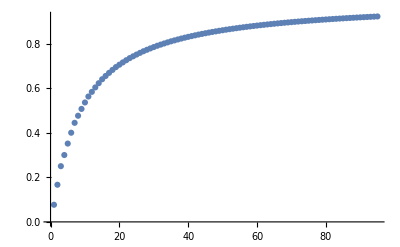

```mathematica
Table[Max[ProcessShort[k]]/Max[ProcessShort2[k]],{k,6,100}]//ListPlot
```

```mathematica
vals={1,2,4,6,9,12,17,21,28,33,44,50,65,72,94,102,132,141,183,193,249,260,337,349,450,463,598,612,788,803,1034,1050,1347,1364,1749,1767,2257,2276,2903,2923,3715,3736,4738,4760,6015,6038,7613,7637,9595}
```

{1,2,4,6,9,12,17,21,28,33,44,50,65,72,94,102,132,141,183,193,249,260,337,349,450,463,598,612,788,803,1034,1050,1347,1364,1749,1767,2257,2276,2903,2923,3715,3736,4738,4760,6015,6038,7613,7637,9595}

```mathematica
Mark[range_,val_]:=Map[If[#==val,Style[#,Red,Bold],#]&,range]
```

```mathematica
Filter[range_,val_]:=Select[range,#==val&]
```

```mathematica
Table[Filter[ProcessShort[k],vals[[k-5]]],{k,6,50}]//TableForm
```

1 |  | 
2 |  | 
4 |  | 
6 |  | 
9 | 9 | 
12 |  | 
17 |  | 
21 |  | 
28 |  | 
33 |  | 
44 |  | 
50 |  | 
65 | 65 | 65
72 | 72 | 72
94 |  | 
102 | 102 | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  |